Diplomado En Programación Básica
Universidad Autónoma de Chiapas
Centro Mesoamericano de Física Teórica

Michael Steven Paucar Rojas

# MATHEMATICA

-Graphics-

## 1. Introducción

El presente cuaderno constituye un recurso de apoyo para el aprendizaje de Mathematica orientado a la programación y al uso de sus principales funciones en contextos académicos y prácticos. El contenido se organiza de manera progresiva iniciando con operaciones básicas sobre listas, expresiones matemáticas y representaciones gráficas para avanzar hacia temas más complejos como manejo de entidades, conversiones de unidades, generación de visualizaciones interactivas y aplicaciones en análisis de datos.

El enfoque seguido combina teoría con ejemplos prácticos que buscan ilustrar no solo la sintaxis del lenguaje sino también la lógica detrás de cada comando. Se ha procurado mantener una estructura clara donde cada sección incluye subtítulos, descripciones y comentarios en el código para facilitar la comprensión. Esto permite que el material pueda ser utilizado tanto por estudiantes en formación como por interesados en explorar las capacidades del software en distintos escenarios.

Cabe señalar que el documento reúne apuntes propios sistematizados a partir del estudio y la práctica personal. Estos apuntes no reemplazan la documentación oficial de Mathematica pero sí constituyen un complemento útil para guiar el aprendizaje y servir como referencia en la resolución de ejercicios y proyectos futuros.

## 2. Tabla de contenidos

Introducción

Tabla de contenidos

Clase 1 — Introducción a Wolfram Mathematica

Captura y análisis de imagen

Clase 2 — Comandos básicos, listas y entidades

Comandos del sistema

Comandos interactivos

Entidades: países y banderas

Exploración planetaria

Conversiones de unidades y monedas

Listas: creación y operaciones básicas

Funciones para secuencias y combinación de listas

Manipulación avanzada de listas

Funciones adicionales sobre listas

Clase 3 — Gráficos, colores y funciones trigonométricas

Gráficas estadísticas (barras y pastel)

Selección y manipulación de datos para visualización

Colores y estilos gráficos (paletas y transformaciones)

Funciones matemáticas básicas y plots elementales

Clase 4 — Funciones  Trascendentes

Expansión de expresiones trigonométricas

Números complejos

Logaritmos

Exponenciales

Series

Límites

Funciones

Derivadas

Integrales

Notación de Lagrange

Integración Numérica

Tablas

Gráfica de Tablas

Clase 5 — Visualización matemática interactiva

Gráficas Bidimensionales (2D)

Gráficas Tridimensionales (3D)

7.3 Manipuladores Interactivos

Tareas

Tarea 1 — Cálculos Numéricos y Funciones en Mathematic

Tarea 2 — Formato de Notebook

Apéndice

Comandos comunes

## 3. Clase 1 — Introducción a Wolfram Mathematica

📆 2025/09/17

⚡ Introducción:

Esta primera clase marca el inicio del estudio sistemático de programación y computación simbólica en Wolfram Mathematica. Su propósito es brindar al estudiante un panorama general del entorno, la sintaxis y la filosofía de trabajo del lenguaje Wolfram. Se exploran las principales características de la interfaz, los modos de evaluación de celdas, y la estructura de los cuadernos interactivos (notebooks), que permiten combinar código, texto y visualizaciones de forma dinámica.

Un aspecto distintivo de esta clase es la introducción al manejo de imágenes digitales. Mathematica permite importar, procesar y analizar imágenes utilizando herramientas integradas. Esto se convierte en una poderosa ventaja al trabajar con proyectos de visualización, visión por computadora y análisis de datos. El alumno aprenderá a extraer información visual (canales de color, bordes, histogramas, etc.) directamente desde imágenes en distintos formatos.

Con esta base, el estudiante estará preparado para abordar tareas más avanzadas en computación matemática, programación estructurada y análisis simbólico en clases posteriores.

📘 Objetivos de la clase:

Conocer el entorno y las funcionalidades principales de Mathematica.

Aprender a importar y manipular imágenes dentro del entorno.

Realizar operaciones básicas de análisis sobre imágenes: extracción de color, bordes, canales, entre otros.

Familiarizarse con la evaluación de celdas, edición de texto y estructura del cuaderno.

Entender cómo almacenar y reutilizar resultados computacionales.

## 3.1. Captura y análisis de imagen

📌 Explicación: Se muestra cómo capturar una imagen desde la cámara (CurrentImage) y cómo aplicar una función de análisis facial (FacialFeatures).

Para detalles de CurrentImage y FacialFeatures ver ‘Comandos comunes’.

# Capturar imagen desde la cámara

```mathematica
yo=CurrentImage[]
```

-Graphics-

# Detectar rasgos faciales en la imagen

```mathematica
FacialFeatures[yo]
```

{<|Image→-Graphics-,Age→24,Gender→Female,Emotion→neutral|>}

💎 Nota: El análisis facial proporciona una edad aproximada y puede intentar identificar el género de la persona en la imagen. Sin embargo, los resultados pueden no ser precisos, y es posible que se necesiten varios intentos para obtener una estimación más acertada.

## 4. Clase 2 — Comandos básicos, listas y entidades

📆 2025/09/22

⚡ Introducción:

En esta clase se profundiza en los aspectos fundamentales del lenguaje de Wolfram Mathematica, con énfasis en el uso de comandos básicos, estructuras de datos esenciales como listas, y la exploración de entidades semánticas. Estos tres pilares permiten al estudiante desarrollar habilidades en la manipulación estructurada de información, automatización de tareas y acceso a bases de datos computacionales integradas.

Los comandos del sistema proporcionan acceso a configuraciones internas, mientras que las funciones interactivas permiten crear contenidos visuales dinámicos como controles deslizantes, selectores y entradas dependientes del usuario. A través de estos elementos, se introducen herramientas de visualización, modelado y simulación básica.

Por otro lado, el uso de entidades semánticas (como países, monedas, unidades físicas, cuerpos astronómicos, entre otros) permite operar con datos reales y estructurados, sin necesidad de definir cada elemento manualmente. Esta característica convierte a Mathematica en una plataforma especialmente útil para proyectos de ciencia aplicada, educación y análisis de información contextual.

Finalmente, se abordan técnicas de creación, combinación, transformación y filtrado de listas, permitiendo al alumno adquirir herramientas para el tratamiento de colecciones de datos —una habilidad clave para cualquier trabajo computacional.

📘 Objetivos de la clase:

Dominar comandos del sistema y funciones interactivas comunes.

Manipular listas: creación, acceso, combinaciones y transformaciones.

Utilizar entidades integradas del sistema (países, unidades, monedas, planetas).

Aplicar funciones para exploración astronómica y conversión de datos.

Resolver problemas prácticos con estructuras de datos y secuencias.

## 4.1. Comandos del sistema

📌 Explicación: Funciones para fijar directorio de trabajo y consultar la fecha/hora del sistema.

Ver Comandos comunes para definiciones.

# Suma básica a través del teclado

```mathematica
2+2
```

4

# Entrada desde la paelta de Wolfram Mathematica

```mathematica
2^4
```

16

# Entrada fracción

```mathematica
6/3
```

2

# Muestra la ruta del directorio de trabajo actual.

```mathematica
Directory[]
```

C:\Users\IBM

# Define o consulta el directorio de trabajo

```mathematica
SetDirectory[]
```

C:\Users\IBM

# Devuelve fecha y hora actual

```mathematica
Date[]
```

{2025,9,23,22,46,39.8336576}

# Devuelve una lista de nombres de archivos en el directorio actual.

```mathematica
FileNames[]
```

{-1.14-windows.xml,3D Objects,.anaconda,AppData,Apple,Application Data,Autodesk,.bash_history,.cache,Cisco Packet Tracer 8.0.1,.conda,.condarc,.config,Contacts,Cookies,Desktop,Documents,Downloads,Dropbox,.eclipse,eclipse,eclipse-workspace,Favorites,git,.gitconfig,.git-for-windows-updater,GNS3,.gradle,.icesoft,IntelGraphicsProfiles,.ipython,.lesshst,Links,Local Settings,.m2,.matplotlib,MicrosoftEdgeBackups,.minttyrc,.ms-ad,Music,My Documents,NetHood,NTUSER.DAT,NTUSER.DAT{13d239bc-378a-11ed-8537-8086f294e387}.TM.blf,NTUSER.DAT{13d239bc-378a-11ed-8537-8086f294e387}.TMContainer00000000000000000001.regtrans-ms,NTUSER.DAT{13d239bc-378a-11ed-8537-8086f294e387}.TMContainer00000000000000000002.regtrans-ms,NTUSER.DAT{3213189e-49df-11ed-853d-8086f294e387}.TM.blf,NTUSER.DAT{3213189e-49df-11ed-853d-8086f294e387}.TMContainer00000000000000000001.regtrans-ms,NTUSER.DAT{3213189e-49df-11ed-853d-8086f294e387}.TMContainer00000000000000000002.regtrans-ms,NTUSER.DAT{7099f723-d717-11ec-8523-8086f294e387}.TM.blf,NTUSER.DAT{7099f723-d717-11ec-8523-8086f294e387}.TMContainer00000000000000000001.regtrans-ms,NTUSER.DAT{7099f723-d717-11ec-8523-8086f294e387}.TMContainer00000000000000000002.regtrans-ms,NTUSER.DAT{7612446a-91d2-11eb-84e0-dd14c26d8a4b}.TM.blf,NTUSER.DAT{7612446a-91d2-11eb-84e0-dd14c26d8a4b}.TMContainer00000000000000000001.regtrans-ms,NTUSER.DAT{7612446a-91d2-11eb-84e0-dd14c26d8a4b}.TMContainer00000000000000000002.regtrans-ms,NTUSER.DAT{b6e954ee-351e-11ed-8535-8086f294e387}.TM.blf,NTUSER.DAT{b6e954ee-351e-11ed-8535-8086f294e387}.TMContainer00000000000000000001.regtrans-ms,NTUSER.DAT{b6e954ee-351e-11ed-8535-8086f294e387}.TMContainer00000000000000000002.regtrans-ms,NTUSER.DAT{fb3e151d-2771-11ee-8588-8086f294e38b}.TM.blf,NTUSER.DAT{fb3e151d-2771-11ee-8588-8086f294e38b}.TMContainer00000000000000000001.regtrans-ms,NTUSER.DAT{fb3e151d-2771-11ee-8588-8086f294e38b}.TMContainer00000000000000000002.regtrans-ms,ntuser.dat.LOG1,ntuser.dat.LOG2,ntuser.ini,OneDrive,.openjfx,.p2,.packettracer,Pictures,PrintHood,projects,.pylint.d,Recent,.redhat,Roaming,Saved Games,.scm_gui,.scm_guirc,Searches,SendTo,.spss,spyder_crash.log,Start Menu,Templates,Videos,.VirtualBox,VirtualBox VMs,.vscode,.vscode-R,zinjai}

## 4.2. Comandos interactivos

📌 Explicación: Salida de voz y botones interactivos para respuestas en tiempo real.

# Convierte el texto a audio y reproduce “Hola Mundo”

```mathematica
Speak["Hola Mundo"]
```

# Reproduce “Hello Wolfram” mediante síntesis de voz

```mathematica
Speak["Hello Wolfram"]
```

# Crea un botón que al presionarlo ejecuta Speak[“Thank you”]

```mathematica
Button["Presioname", Speak[Thank You]]
```

Presioname

💎 Nota: Button crea controles interactivos; ejecuta la acción cuando se presiona. 
Ver ‘Comandos comunes’ para más usos de Button y Speak.

## 4.3. Entidades: países y banderas

📌 Explicación:  Uso de la Wolfram Knowledgebase Entity para recuperar información de países y sus banderas.

# Crea la entidad correspondiente al país’Ecuador’

```mathematica
Entity["Country", "Ecuador"]
```

Ecuador

# Extrae la imagen de la bandera de la entidad país

```mathematica
Entity["Country", "Ecuador"]["Flag"]
```

-Graphics-

# Devuelve una lista de imágenes/flags para los países listados.

```mathematica
EntityValue[{Entity["Country", "UnitedStates"], Entity["Country", "Brazil"], Entity["Country", "China"]}]
```

{Estados Unidos,Brasil,República Popular China}

# Obtener banderas de múltiples países


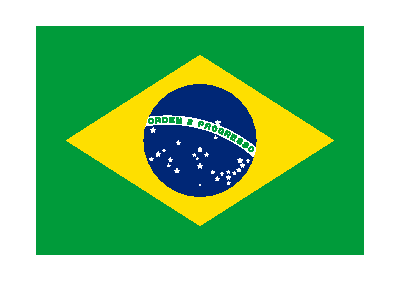

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[{Entity["Country", "UnitedStates"], Entity["Country", "Brazil"], Entity["Country", "Ecuador"], Entity["Country", "China"],Entity["Country", "Mexico"]}, "Flag"]
```

## 4.4. Exploración planetaria

📌 Explicación:  Listar entidades de tipo planeta y recuperar sus imágenes u otras propiedades.

# Lista todas las entidades que pertenecen a la clase’Planet’

```mathematica
EntityList[EntityClass["Planet", All]]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

# Recupera la imagen asociada a cada planeta listado

```mathematica
EntityValue[EntityClass["Planet", All], "Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 4.5. Conversiones de unidades y monedas

📌 Explicación: Trabajo con Quantity y UnitConvert para convertir y simplificar unidades; CurrencyConvert para divisas.

# Convierte 2.6 horas a minutos

```mathematica
UnitConvert[Quantity[2.6,  "Hours"], "Minutes"]
```

156. min

# Suma cantidades con unidades distintas;Mathematica maneja la conversión interna

```mathematica
Quantity[7.5, "Feet"] + Quantity[14, "Centimeters"]
```

242.6 cm

# Simplifica la unidad si es posible (ej.:a metros)

```mathematica
UnitSimplify[Quantity[242.6, "Centimeters"]]
```

2.426 m

# Convierte 100 liras turcas a USD usando tasa actual;puede requerir conexión

```mathematica
CurrencyConvert[Quantity[100., "TRY"], Quantity[1, "USDollars"]]
```

2.41 $

# Convierte dólares a centavos estadounidenses

```mathematica
UnitConvert[Quantity[5.12363, "USDollars"], "USCents"]
```

512.363 ¢

# Convierte 5 pulgadas a centímetros y devuelve número aproximado

```mathematica
N[UnitConvert[Quantity[5, "Inches"], "Centimeters"]]
```

12.7 cm

💎 Nota: CurrencyConvert puede necesitar conexión a internet para obtener tipos de cambio actualizados.

## 4.6. Listas: creación y operaciones básicas

📌 Explicación: Definición de listas, operaciones escalares, limpieza de variables y gráficas sencillas.

📋 Declaración de listas:

{} (llaves) → Sirven para definir listas.

```mathematica
lista={2,4,6,8}
```

{2,4,6,8}

Sin llaves → Se usa cuando una función espera un rango o expresión directamente, no un conjunto de valores.

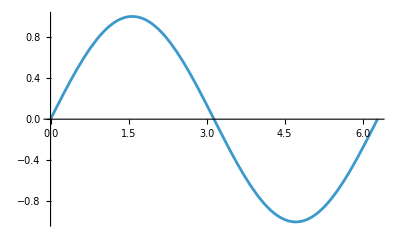

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

Aquí los límites {x,0,2 Pi} son un rango, no una lista de valores discretos.

🔒 Regla práctica:

Usa llaves {} cuando quieras pasar conjuntos de valores discretos ({1,2,3}).

Usa sin llaves o rangos {var,min,max} cuando definas un intervalo continuo.

# Elimina cualquier valor previo de la variable a

```mathematica
Clear[a]
```

# Asigna una lista a ’a’

```mathematica
a = {2, 6, 8, 9, 10}
```

{2,6,8,9,10}

# Asigna una lista a ’b’

```mathematica
b = {5, 8, 9, 5}
```

{5,8,9,5}

# Escalar por lista

```mathematica
3 * a
```

{6,18,24,27,30}

```mathematica
Clear[a]
```

```mathematica
a
```

a

```mathematica
a * 5
```

5 a

# Grafica los valores de la lista como puntos/serie

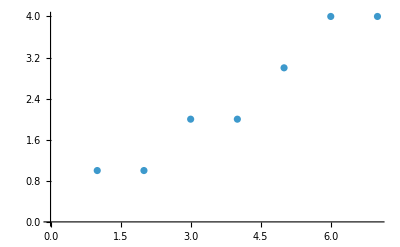

```mathematica
ListPlot[{1, 1, 2, 2, 3, 4, 4}]
```

# Gráfico mejorado  con los valores de la lista como puntos/serie

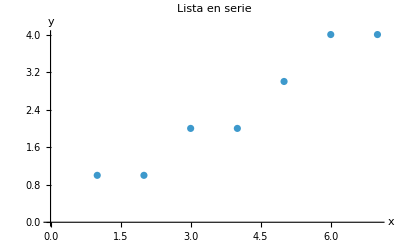

```mathematica
Show[%33,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[Lista en serie],LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0],Italic}]
```

## 4.7. Funciones para secuencias y combinación de listas

📌 Explicación: Generar rangos, invertir, unir listas y visualizar secuencias.

Ver ‘Comandos comunes’ para información sobre Range, Join y Reverse.

```mathematica
?Range
```

⭐ El ‘?comando’, muestra la ayuda o documentación para la función Range.

# Genera la lista {1,2,...,25}

```mathematica
Range[25]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

# Grafica la secuencia 1..20

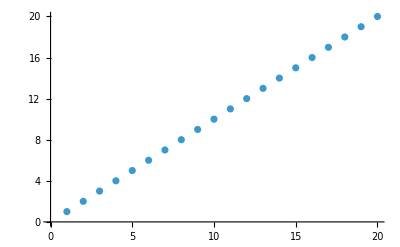

```mathematica
ListPlot[Range[20]]
```

# Invierte el orden:devuelve {4,3,2,1}

```mathematica
Reverse[{1, 2, 3, 4}]
```

{4,3,2,1}

# Une dos listas:{1,2,3,6}

```mathematica
Join[{1, 2, 3}, {6}]
```

{1,2,3,6}

📌 Explicación:  Join concatena listas sin eliminar duplicados; para obtener unión única usa Union.

# Une {1,2,3} con {1,2,3,4,5}->{1,2,3,1,2,3,4,5}

```mathematica
Join[Range[3], Range[5]]
```

{1,2,3,1,2,3,4,5}

🎯 Reto en clase — Listas
Resolver los ejercicios con funciones de Listas.

Salida esperada {1, 2, 3, 4, 5, 3, 2, 1, 10, 15}

# Función Join:
	# La función `Join` se utiliza para combinar varias listas en una sola.

# Rango de números (Range):
	# `Range[5]` genera una lista de números desde 1 hasta 5, es decir, {1, 2, 3, 4, 5}.
	# `Reverse[Range[3]]` primero genera la lista {1, 2, 3} y luego la invierte, resultando en {3, 2, 1}.
	# `{10, 15}` es simplemente una lista con los números 10 y 15.

# Resultado:
	# El resultado de `Join` es la combinación de las tres listas mencionadas:
	# {1, 2, 3, 4, 5}, {3, 2, 1} y {10, 15}.
	# La lista final será: {1, 2, 3, 4, 5, 3, 2, 1, 10, 15}.

```mathematica
Join[Range[5], Reverse[Range[3]], {10, 15}]
```

{1,2,3,4,5,3,2,1,10,15}

Salida esperada {5, 6, 7, 8, 1, 2, 4, 5, 4, 3}

# Función Join:
	# La función `Join` se utiliza para combinar varias listas en una sola.

# Rango de números (Range):
	# `Range[5, 8]` genera una lista de números desde 5 hasta 8, es decir, {5, 6, 7, 8}.
	# `Range[5]` genera una lista de números desde 1 hasta 5, es decir, {1, 2, 3, 4, 5}.
	# `{4, 3}` es una lista con los números 4 y 3.

# Resultado:
	# El resultado de `Join` es la combinación de las tres listas mencionadas:
	# {5, 6, 7, 8}, {1, 2, 3, 4, 5} y {4, 3}.
	# La lista final será: {5, 6, 7, 8, 1, 2, 3, 4, 5, 4, 3}.

```mathematica
Join[Range[5,8], Range[5], {4, 3}]
```

{5,6,7,8,1,2,3,4,5,4,3}

💎 Nota: También se puede ordenar, contar repeticiones (Count), graficar (ListPlot), extraer sublistas (Take, Drop).

## 4.8. Manipulación avanzada de listas

📌 Explicación: Técnicas para construir listas complejas y comprobar pertenencia o patrones.

# Crea lista combinada:{1,2,3,6}

```mathematica
list = Join[{1, 2, 3}, {6}]
```

{1,2,3,6}

# Devuelve True si 6 está en ’list’

```mathematica
MemberQ[list, 6]
```

True

# Construye una lista concatenando transformaciones de Range

```mathematica
Join[Range[4] + 4, Range[2], Range[2] + 3, {3}]
```

{5,6,7,8,1,2,4,5,3}

# Variante que incluye Reverse para cambiar orden de una parte

```mathematica
Join[Range[4] + 4, Range[2], Range[2] + 3, Reverse[Range[2]+2]]
```

{5,6,7,8,1,2,4,5,4,3}

# Grafica la concatenación de tres secuencias 1..20 (serie repetida)

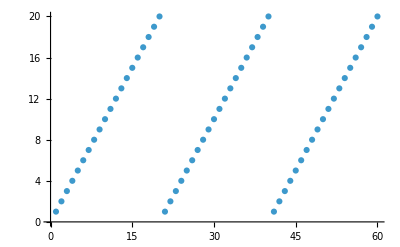

```mathematica
ListPlot[Join[Range[20], Range[20], Range[20]]]
```

## 4.9. Funciones adicionales sobre listas

📌 Explicación: Varias funciones pequeñas pero muy útiles para análisis rápido de listas y números.

Funciones útiles: conteo, orden, extracción.

# Genera la lista 1..100

```mathematica
Range[10^2]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

# Ordena la lista ascendentemente

```mathematica
Sort[{4, 2, 1, 3, 6}]
```

{1,2,3,4,6}

# Devuelve la longitud de la lista

```mathematica
Length[{5, 4, 5, 3, 4, 5}]
```

6

# Suma todos los elementos de la lista

```mathematica
Total[{1, 2, 2, 2}]
```

7

# Suma 1..10->55

```mathematica
Total[Range[10]]
```

55

# Cuenta cuántas veces aparece’b’ (simbolos/elementos)

```mathematica
Count[{a, a, a, a, c, b, a}, b]
```

1

# Devuelve el primer elemento

```mathematica
First[{7, 6, 5}]
```

7

# Devuelve el último elemento

```mathematica
Last[{7, 6, 5}]
```

5

# Ordena y devuelve el primero (mínimo)

```mathematica
First[Sort[{6, 7, 1, 2, 4, 5}]]
```

1

# Devuelve el mínimo de la lista

```mathematica
Min[{6, 7, 1, 2, 4, 5}]
```

1

# Devuelve {1,9,8,8}

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

# Devuelve el último dígito:8

```mathematica
Last[IntegerDigits[1988]]
```

8

# Crea {1,2,3,4,4,3,2,1} con Join

```mathematica
Join[Range[4], Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

# Genera una secuencia 1..k con k aleatorio entre 0 y 30

```mathematica
Range[RandomInteger[30]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

💎 Nota: Estas funciones son atómicas para análisis y resumen de datos; úsalas dentro de pipelines con Map, Select y Fold para tareas más avanzadas.

## 5. Clase 3 — Gráficos, colores y funciones trigonométricas

📆 2025/09/17

⚡ Introducción:

Esta clase se centra en las capacidades de Mathematica para la generación de gráficos y visualizaciones matemáticas. Se introducen tanto gráficos estadísticos como funciones matemáticas, incluyendo herramientas para la representación visual personalizada mediante estilos, colores y leyendas. El objetivo es capacitar al estudiante para producir visualizaciones claras, comprensibles y estéticamente cuidadas, integrando elementos visuales con contenido analítico.

Se estudian gráficos de barras y pastel a partir de datos simples o estructurados, destacando opciones de estilo, disposición y etiquetado. También se exploran las paletas de color, que permiten resaltar visualmente categorías, intensidades o agrupaciones. Estas herramientas son fundamentales en el diseño de presentaciones, informes técnicos y análisis exploratorio de datos.

En la segunda parte, se introducen las funciones trigonométricas (sin, cos, tan) como ejemplos clave de funciones periódicas. A través de gráficos de funciones y sus respectivas áreas sombreadas, el estudiante comprenderá visualmente conceptos fundamentales como amplitud, periodo y desfase. Además, se explican herramientas para graficar múltiples funciones simultáneamente, superponer estilos diferentes y destacar intersecciones o regiones de interés.

Esta clase proporciona un puente entre el cálculo matemático y la visualización efectiva de funciones, preparando al alumno para análisis más avanzados en clases futuras.

📘 Objetivos de la clase:

Crear gráficos estadísticos básicos con personalización visual.

Usar paletas de color y estilos para mejorar la visualización de datos.

Graficar funciones matemáticas básicas y trigonométricas.

Utilizar funciones de sombreado y leyendas automáticas.

Relacionar representaciones gráficas con propiedades analíticas.

## 5.1. Gráficas estadísticas (barras y pastel)

📌 Explicación: Ejemplos con BarChart y PieChart en 2D y 3D.

Útiles para visualizar distribuciones de frecuencia o categorías.

📊 Opciones de gráficos
Las funciones gráficas (PieChart, BarChart, Plot, etc.) aceptan opciones para personalizar estilo, etiquetas y apariencia.

```mathematica
PieChart3D[{8,9,6,8,1,3,7,4},ChartElementFunction->"CylindricalSector3D",ChartStyle->{Red,Purple,Green,Blue,Orange,Yellow,Cyan,Gray},ChartLegends->{"Rojo","Morado","Verde","Azul","Naranja","Amarillo","Cian","Gris"}]
```

-Graphics3D-

📌 Explicación:

ChartElementFunction -> “CylindricalSector3D” → Cambia la forma del sector en 3D.

ChartStyle -> {...} → Aplica colores definidos a cada porción.

ChartLegends -> {...} → Añade leyendas personalizadas con etiquetas.

🎨 Estilo de texto y fuentes: Style[texto, opciones] — Cambia fuente, tamaño, color, etc.

```mathematica
Style["Texto en azul y grande",Blue,18,Bold]
```

Texto en azul y grande

🔎 Opciones comunes:

FontSize -> n

FontColor -> Color

FontFamily -> “Arial”

Bold, Italic

# En gráficos, puedes integrarlo en etiquetas y títulos

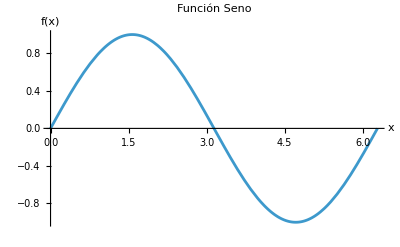

```mathematica
Plot[Sin[x],{x,0,2 Pi},PlotLabel->Style["Función Seno",16,Bold,Blue],AxesLabel->{Style["x",14],Style["f(x)",14,Italic]}]
```

🏷️ Etiquetas en gráficos:

PlotLabel -> “texto” → Título del gráfico.

AxesLabel -> {“x”,”y”} → Nombres de ejes.

ChartLegends -> {“etiqueta1”,”etiqueta2”,...} → Leyendas para gráficos de sectores o barras.

LabelStyle -> {...} → Cambia estilo de todas las etiquetas del gráfico.

# Mínimo de la lista;uso previo para resumen

```mathematica
Min[{8, 9, 6, 8, 1, 3, 7, 4}]
```

1

# Gráfico de barras 2D de la lista

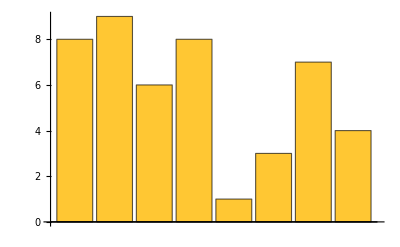

```mathematica
BarChart[{8, 9, 6, 8, 1, 3, 7, 4}]
```

# Este código genera un gráfico de barras con un título y estilo de etiquetas personalizado.
	# Título del gráfico: “Gráfico de Barras”
		# Añade un título al gráfico usando la opción PlotLabel.
		# El título es una expresión que se presenta como “Gráfico de Barras”.
  
	# Estilo de las etiquetas: 
		# Establece el estilo de las etiquetas con un tipo de fuente y tamaño específico.
		# FontFamily -> “Roboto Serif” define el tipo de letra.
		# 20pt es el tamaño de la fuente para las etiquetas.
		# GrayLevel[0] establece el color de las etiquetas a un gris oscuro (nivel de gris 0 es negro).

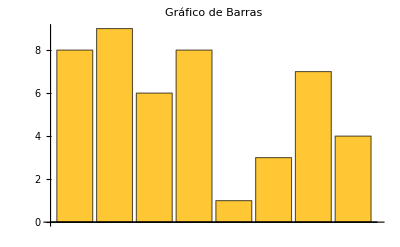

```mathematica
Show[%1,PlotLabel->HoldForm[Gráfico de Barras],LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

# Gráfico de barras en 3D (visual)

```mathematica
BarChart3D[{8, 9, 6, 8, 1, 3, 7, 4}]
```

-Graphics3D-

# Gráfico de barras 3D:
	# Se genera un gráfico de barras en 3D utilizando la función `BarChart3D`.
	# Los valores de las barras son: {8, 9, 6, 8, 1, 3, 7, 4}.
	# Estos valores representan la altura de cada barra en el gráfico 3D.

# Configuración de la forma de las barras:
	# La opción `ChartElementFunction -> “Cylinder”` modifica la forma de las barras.
	# En lugar de las barras rectangulares estándar, se utiliza la forma de cilindro.

```mathematica
BarChart3D[{8,9,6,8,1,3,7,4},ChartElementFunction->"Cylinder"]
```

-Graphics3D-

# Gráfico de pastel 2D

```mathematica
PieChart[{8, 9, 6, 8, 1, 3, 7, 4}]
```

-Graphics-

# Gráfico de pastel 2D
	# Se genera un gráfico de tarta (pie chart) con los valores: {8, 9, 6, 8, 1, 3, 7, 4}.
	# Estos valores representan el tamaño de cada sector en la gráfica.

# Función de elementos de gráfico:
	# La opción `ChartElementFunction -> “SquareWaveSector”` cambia la forma de los sectores del gráfico.
	# En lugar de los sectores tradicionales, se utiliza una forma tipo “SquareWave” (onda cuadrada) para los sectores.

# Leyendas del gráfico:
	# `ChartLegends` se usa para añadir leyendas a los sectores.
	# Se asignan etiquetas a cada sector, como “Rojo”, “Morado”, “Verde”, etc.
	# Cada leyenda está estilizada con un color específico (Red, Purple, Green, etc.), utilizando la función `Style` para dar formato a los textos.

# Estilo de los sectores:
	# `ChartStyle` define los colores de cada sector en el gráfico.
	# Los colores asignados son: Red, Purple, Green, Blue, Orange, Yellow, Purple, Gray.
	# Esto cambia el color de cada sector para que coincidan con las leyendas correspondientes.

```mathematica
PieChart[{8,9,6,8,1,3,7,4},ChartElementFunction->"SquareWaveSector",ChartLegends->{Style["Rojo",Red],Style["Morado",Purple],Style["Verde",Green],Style["Azul",Blue],Style["Naranja",Orange],Style["Amarillo",Yellow],Style["Violeta",Purple],Style["Gris",Gray]},ChartStyle->{Red,Purple,Green,Blue,Orange,Yellow,Purple,Gray}]
```

-Graphics-

# Gráfico de pastel 2D

# Título del gráfico:
	# La opción `PlotLabel` se utiliza para asignar un título al gráfico.
	# El título “Gráfico de Pastel” es mostrado en el gráfico.
	# Se usa `HoldForm` para evitar que la expresión se evalúe y se muestre tal cual.

# Estilo de las etiquetas:
	# `LabelStyle` configura el estilo visual de las etiquetas del gráfico.
	# `FontFamily -> “Roboto Serif”` define la fuente a utilizar en las etiquetas.
	# `20pt` es el tamaño de la fuente para las etiquetas.
	# `14` es el tamaño de la fuente para el texto de las etiquetas.
	# `GrayLevel[0]` define el color de las etiquetas como negro.
	# `Bold` aplica el estilo en negrita a las etiquetas, haciendo que el texto se destaque.

```mathematica
Show[%11,PlotLabel->HoldForm[Gráfico de Pastel],LabelStyle->{FontFamily->"Roboto Serif 20pt",14,GrayLevel[0],Bold}]
```

-Graphics-

# Gráfico de pastel en 3D;efecto visual,no recomendado para análisis

```mathematica
PieChart3D[{8, 9, 6, 8, 1, 3, 7, 4}]
```

-Graphics3D-

# Gráfico de tarta 3D:
	# Se genera un gráfico de tarta 3D utilizando la función `PieChart3D`.
	# Los valores de las porciones son: {8, 9, 6, 8, 1, 3, 7, 4}.
	# Cada valor representa el tamaño de una porción del gráfico 3D.

# Función de los elementos de gráfico:
	# `ChartElementFunction -> “CylindricalSector3D”` cambia la forma de los sectores a una forma cilíndrica 3D.
	# Esto crea una visualización tridimensional de los sectores con una forma cilíndrica.

# Estilo de los sectores:
	# `ChartStyle` define los colores de cada sector en el gráfico 3D.
	# Los colores asignados son: Red, Purple, Green, Blue, Orange, Yellow, Cyan, Gray.
	# Cada uno de estos colores corresponde a una de las porciones del gráfico.

# Leyendas del gráfico:
	# `ChartLegends` se utiliza para agregar leyendas personalizadas.
	# Las leyendas indican el color de cada sector, con los nombres: “Rojo”, “Morado”, “Verde”, etc.

```mathematica
PieChart3D[{8,9,6,8,1,3,7,4},ChartElementFunction->"CylindricalSector3D",ChartStyle->{Red,Purple,Green,Blue,Orange,Yellow,Cyan,Gray},ChartLegends->{"Rojo","Morado","Verde","Azul","Naranja","Amarillo","Cian","Gris"}]
```

-Graphics3D-

💎 Nota: Los gráficos 3D son vistosos pero menos precisos para interpretación cuantitativa; para reportes prefiero 2D con etiquetas claras (ChartLabels, PlotLegends).

## 5.2. Selección y manipulación de datos para visualización

📌 Explicación: Funciones para preparar subconjuntos de datos antes de graficar (Take, Drop, Reverse) y trazados auxiliares (NumberLinePlot, Column).

# Devuelve la lista de dígitos de 1988:{1,9,8,8}

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

# Devuelve el último dígito:8

```mathematica
Last[IntegerDigits[1988]]
```

8

# Invierte la lista de dígitos

```mathematica
Reverse[IntegerDigits[1988]]
```

{8,8,9,1}

# Toma los primeros 4 elementos

```mathematica
Take[{101, 203, 401, 602, 332, 412}, 4]
```

{101,203,401,602}

# Elimina los primeros 4 elementos,devuelve el resto

```mathematica
Drop[{101, 203, 401, 602, 332, 412}, 4]
```

{332,412}

# Dibuja puntos en una recta numérica (útil para eventos)

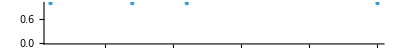

```mathematica
NumberLinePlot[{1, 7, 11, 25}]
```

# Dibuja puntos en una recta numérica (mejorado)

# Ejes del gráfico:
	# La opción `AxesLabel -> {HoldForm[t], None}` se utiliza para etiquetar los ejes.
	# El eje x está etiquetado con “t”, mientras que el eje y no tiene etiqueta (None).
	# `HoldForm` evita que el símbolo de “t” se evalúe y se presenta tal cual.

# Título del gráfico:
	# La opción `PlotLabel -> HoldForm[Crecimiento Bacteriano]` añade un título al gráfico.
	# El título “Crecimiento Bacteriano” es mostrado en el gráfico.
	# Se usa `HoldForm` para evitar la evaluación de la expresión y se visualiza directamente.

# Estilo de las etiquetas:
	# `LabelStyle` se utiliza para definir el estilo de las etiquetas del gráfico.
	# `FontFamily -> “Roboto Serif”` especifica la fuente de las etiquetas.
	# `20pt` es el tamaño de la fuente para las etiquetas, haciendo que el texto sea legible.
	# `GrayLevel[0]` pone el color de las etiquetas en negro.
	# `Bold` hace que el texto de las etiquetas sea **negrita**, para darle énfasis.

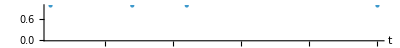

```mathematica
Show[%17,AxesLabel->{HoldForm[t],None},PlotLabel->HoldForm[Crecimiento Bacteriano],LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0],Bold}]
```

# Muestra una columna simple;útil para layout de resultados

```mathematica
Column[{100, 350, 502, 400}]
```

100
350
502
400

💎 Nota:

Preparar la lista (filtrar, normalizar) antes de graficar para evitar picos que deformen la escala.

Usa PlotRange -> All si quieres incluir todos los valores.

# Lista de tres gráficos de pastel:1 pequeño (3 sectores),2 (10 sectores), 3 (20 sectores)
# Para presentar estos gráficos lado a lado conviene usar GraphicsRow[{...}] o GraphicsGrid

```mathematica
{PieChart[Range[3]], PieChart[Range[10]], PieChart[Range[20]]}
```

{-Graphics-,-Graphics-,-Graphics-}

# BarChart: Lista de tres gráficos de barras

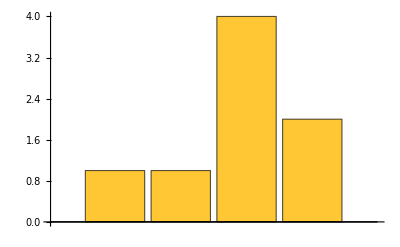
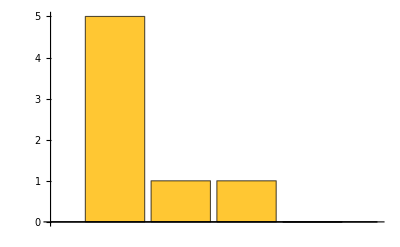
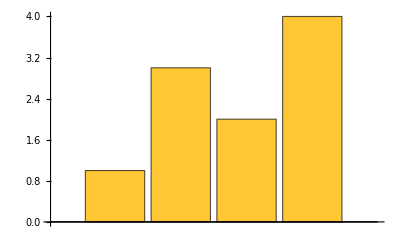

```mathematica
{BarChart[{1, 1, 4, 2}], BarChart[{5, 1, 1, 0}], BarChart[{1, 3, 2, 4}]}
```

## 5.3. Colores y estilos gráficos (paletas y transformaciones)

📌 Explicación: Funciones para generar y transformar colores: RGBColor, Hue, Blend, RandomColor y herramientas para aplicar estilos a textos y gráficos.

# Lista de colores predefinidos

```mathematica
{Red, Green, Blue, Purple, Orange, Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0],GrayLevel[0]}

# Invierte el color azul (negativo) --> Escala cromática

```mathematica
ColorNegate[Blue]
```

RGBColor[1., 1., 0.]

# *Mezcla de colores:amarillo+rojo

```mathematica
Blend[{Yellow, Red}]
```

RGBColor[1, Rational[1, 2], 0]

# Color RGB puro (rojo)

```mathematica
RGBColor[{1, 0, 0}]
```

RGBColor[{1, 0, 0}]

# Color por tono en el espacio HSL

```mathematica
Hue[0.5]
```

Hue[0.5]

# Genera un color aleatorio;útil para pruebas

```mathematica
RandomColor[]
```

RGBColor[0.0378617177385101, 0.41743240473723553, 0.0739950800072493]

# Aplica estilo de color a un texto/número

```mathematica
Style[100, Blue]
```

100

# Texto con tamaño grande

```mathematica
Style[100, 50]
```

100

🎯  Reto en clase — Estilos
Probar diferentes estilos en texto y números.

```mathematica
?Style
```

# Aplica un estilo al número 100 con color naranja,cursiva y tamaño de fuente 32

```mathematica
Style[100, {Orange, Italic, 32}]
```

100

# Aplica un estilo al número 70 con negrita,color rojo,subrayado y tamaño de fuente 20

```mathematica
Style[70, {Bold, Red, Underlined, 20}]
```

70

# Estiliza el texto “Mathematics” con un tamaño de fuente mayor,color púrpura, negrita y tipo de letra

```mathematica
Style["Mathematics",{Larger,Purple,Bold,FontFamily->"Roboto Serif 20pt"}]
```

Mathematics

💎 Nota: Define una paleta al inicio, por ejemplo pal = {RGBColor[...], RGBColor[...], ...}; y úsala en las gráficas con ColorFunction o ChartStyle para consistencia visual.

## 5.4. Funciones matemáticas básicas y plots elementales

📌 Explicación: Evaluación numérica de funciones elementales (coseno, seno), uso de N para aproximaciones y graficado simple con opciones (PlotTheme, PlotRange, AxesLabel).

# Coseno de 0->1

```mathematica
Cos[0]
```

1

# Seno de 0->0

```mathematica
Sin[0]
```

0

# Coseno de π->-1

```mathematica
Cos[Pi]
```

-1

# Forma numérica de Cos[Pi]

```mathematica
N[Cos[π]]
```

-1.

# Aproximación numérica de 10/3

```mathematica
N[10/3]
```

3.33333

# ‘%’ Toma el valor del resultado anterior

```mathematica
%+1
```

4.33333

# Aproximación de Sin(pi/12) con 21 dígitos de precisión

```mathematica
N[Sin[π/12], 21]
```

0.258819045102520762349

# Usa Degree para ángulos en grados

```mathematica
N[Sin[45 Degree]]
```

0.707107

# Salida en radianes

```mathematica
ArcCos[0]
```

π/2

# Tranformación con para salida en grados

```mathematica
N[ArcCos[0]*180/π]
```

90.

🎯 Reto en Clase — Conversión
Input --> Output
rad --> grad (sin conversiones solo con la función Degree)

Entregar la salida del ‘Arccos.08[0]’ en grados

```mathematica
?Degree
```

# Tranformación con “Degree” para salida en grados

```mathematica
N[ArcCos[0]/Degree]
```

90.

# Salida de radianes --> racional

```mathematica
Cos[π/6]
```

(√3)/2

# Salida de radianes --> irracional “N”

```mathematica
N[Cos[π/6]]
```

0.866025

```mathematica
Tan[π/4]
```

1

# Grafica seno en 0..2π

```mathematica
Plot[Sin[x], {x, 0, 2π}]
```

-Graphics-

# Título de la gráfica
# PlotLabel -> “Gráfica de la función Seno”,

# Etiquetas de los ejes
# AxesLabel -> {“x”, “f(x)”},

# Color de la línea de la gráfica
# PlotStyle -> Blue,

# Ticks automáticos en ambos ejes
# Ticks -> {Automatic, Automatic},

# Añadir marco alrededor de la gráfica
# Frame -> True,

# Líneas de la cuadrícula
# GridLines -> Automatic,

# Etiquetas para el marco de la gráfica
# FrameLabel -> {“x”, “f(x)”},

# Ticks automáticos en el marco
# FrameTicks -> {Automatic, Automatic},

# Asegura que toda la función esté visible
# PlotRange -> All

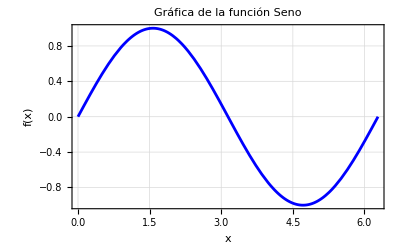

```mathematica
Plot[Sin[x],{x,0,2 π},PlotLabel->"Gráfica de la función Seno",AxesLabel->{"x","f(x)"},PlotStyle->Blue,GridLines->Automatic,Ticks->{Automatic,Automatic},Frame->True,FrameLabel->{"x","f(x)"},FrameTicks->{Automatic,Automatic},PlotRange->All  ]
```

# Grafica coseno en 0..2π

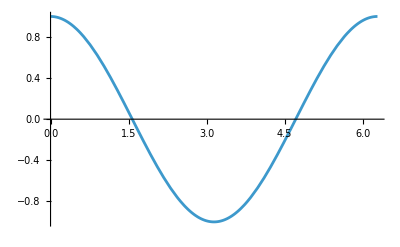

```mathematica
Plot[Cos[x], {x,  0, 2Pi}]
```

# Título de la gráfica
# PlotLabel -> “Gráfica de la función Coseno”,

# Etiquetas de los ejes
# AxesLabel -> {“x”, “f(x)”},

# Color de la línea de la gráfica
# PlotStyle -> Red,

# Ticks automáticos en ambos ejes
# Ticks -> {Automatic, Automatic},

# Añadir marco alrededor de la gráfica
# Frame -> True,

# Líneas de la cuadrícula
# GridLines -> Automatic,

# Etiquetas para el marco de la gráfica
# FrameLabel -> {“x”, “f(x)”},

# Ticks automáticos en el marco
# FrameTicks -> {Automatic, Automatic},

# Asegura que toda la función esté visible
# PlotRange -> All

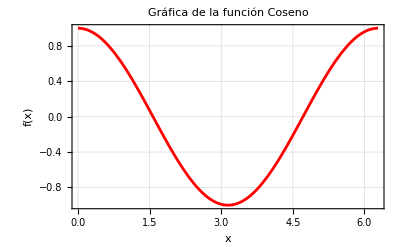

```mathematica
Plot[Cos[x],{x,0,2 π},PlotLabel->"Gráfica de la función Coseno",AxesLabel->{"x","f(x)"},PlotStyle->Red,GridLines->Automatic,Ticks->{Automatic,Automatic},Frame->True,FrameLabel->{"x","f(x)"},FrameTicks->{Automatic,Automatic},PlotRange->All]
```

💎 Nota: Usar AxesLabel -> {HoldForm[x], HoldForm[f(x)]} y ImageSize -> Large para gráficos más presentables al exportar.

🎯 Reto en clase — Funciones trigonométricas normales e inversas
Graficar múltiples funciones trigonométricas en un solo plot; para las funciones inversas conviene limitar dominio/rango para evitar valores complejos o discontinuidades.

Gráficas de Funciones Trigonométricas

# Definir lista de funciones trigonométricas normales

```mathematica
trigonometric = {Sin[x], Cos[x], Tan[x], Sec[x], Csc[x], Cot[x]}
```

{Sin[x],Cos[x],Tan[x],Sec[x],Csc[x],Cot[x]}

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles

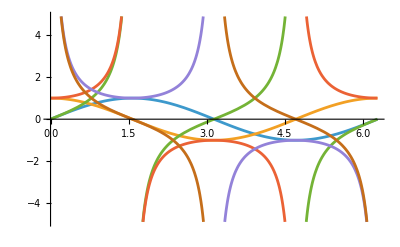

```mathematica
Plot[trigonometric, {x, 0, 2Pi}]
```

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles (mejorado)

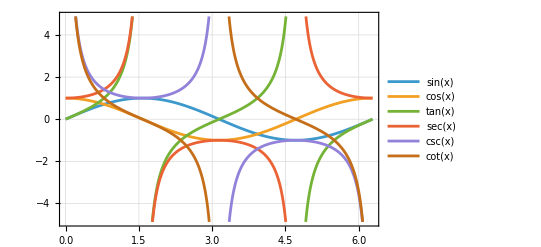

```mathematica
Plot[trigonometric,{x,0,2 π},PlotTheme->"Detailed"]
```

Gráficas de Funciones Trigonométricas Inversas

# Definir lista de funciones trigonométricas inversas

```mathematica
invTri = {ArcSin[x], ArcCos[x], ArcTan[x], ArcSec[x], ArcCsc[x], ArcCot[x]}
```

{ArcSin[x],ArcCos[x],ArcTan[x],ArcSec[x],ArcCsc[x],ArcCot[x]}

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles

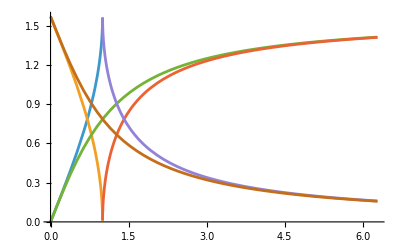

```mathematica
Plot[invTri, {x, 0, 2Pi}]
```

# Graficar todas juntas en 0..2π;PlotRange->All para incluir singularidades visibles (mejorado)

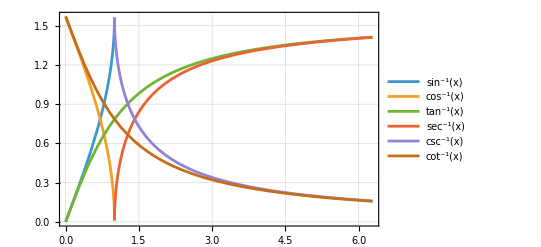

```mathematica
Plot[invTri,{x,0,2 π},PlotTheme->"Detailed"]
```

💎 Nota: Al exportar gráficos para informes use ImageSize->Large y Export con formato PNG o PDF; incluye títulos y etiquetas claras (AxesLabel, PlotLabel) y una leyenda (PlotLegends).

## 6. Clase 4 — Funciones Trascendentes

📆 2025/09/29

⚡ Introducción:

En esta clase se abordará el estudio y la representación computacional de las funciones trascendentes, un conjunto fundamental de funciones que no pueden expresarse únicamente mediante operaciones algebraicas básicas. Estas funciones incluyen, entre otras, a las exponenciales, logarítmicas y trigonométricas, así como sus inversas e hiperbolicas, y tienen un papel central en el análisis matemático y en múltiples aplicaciones científicas y de ingeniería.

A través del uso del software Mathematica, se explorarán métodos para su representación simbólica, gráfica y numérica. Esto incluye la evaluación de límites, el cálculo de derivadas e integrales tanto exactas como aproximadas, y el uso de series de potencias (como las expansiones de Taylor y Maclaurin) para la aproximación local de funciones.

También se trabajará con la notación matemática formal (por ejemplo, 𝑓’(x), ∫f(x)ⅆx etc.), permitiendo al estudiante familiarizarse con el lenguaje riguroso del cálculo diferencial e integral, así como su implementación computacional. Finalmente, se integrarán herramientas de visualización como la graficación de funciones, sombreado de regiones e interpretación de tablas de valores, facilitando una comprensión intuitiva y profunda de estos conceptos.

📘 Objetivos de la clase:

Identificar y clasificar las funciones trascendentes más comunes: exponenciales, logarítmicas y trigonométricas.

Representar funciones trascendentes mediante gráficos y tablas usando Mathematica.

Calcular y visualizar límites, derivadas e integrales simbólicas y numéricas.

Aplicar la notación matemática formal en expresiones y resultados computacionales.

Usar series de potencias (Taylor/Maclaurin) para aproximar funciones trascendentes.

Implementar integración numérica sobre funciones trascendentes.

## 6.1. Expansión de expresiones trigonométricas

📌 Explicación: Uso de TrigExpand para descomponer funciones trigonométricas en sumas o productos, aplicando identidades.

# función... TrigExpand aplica identidades trigonométricas para expandir la expresión

```mathematica
TrigExpand[Sin[x]^2 + Cos[x]^2]
```

1

# TrigReduce reduce funciones trigonométricas a formas más simples o básicas

```mathematica
TrigReduce[Sin[x]/Cos[x]]
```

Tan[x]

# Aplica la identidad de ángulo doble: Sin[2x] → 2 Sin[x] Cos[x]

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

ExpToTrig convierte funciones exponenciales complejas a su forma trigonométrica

```mathematica
ExpToTrig[Exp[-ⅈx]]
```

Cosh[ⅈx]-Sinh[ⅈx]

# TrigFactor factoriza expresiones trigonométricas  
# reescribe Sin[2 z] como 2 Sin[z] Cos[z], utilizando una identidad trigonométrica

```mathematica
TrigFactor[Sin[2 z]]
```

2 Cos[z] Sin[z]

# TrigToExp convierte funciones trigonométricas e hiperbólicas en su forma exponencial  
# Sin[z] → (e^(i z) - e^(-i z)) / (2 i)  
# Cosh[z] → (e^z + e^(-z)) / 2

```mathematica
TrigToExp[{Sin[z], Cosh[z]}]
```

{1/2 ⅈ ⅇ^(-ⅈ z)-1/2 ⅈ ⅇ^(ⅈ z),ⅇ^-z/2+ⅇ^z/2}

# Gráfica del seno con rango (0-10)

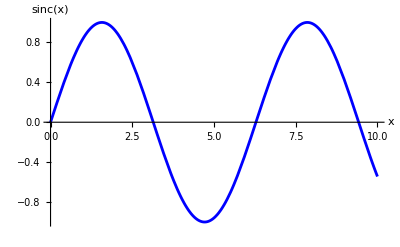

```mathematica
Plot[Sin[x], {x,0 , 10}, AxesLabel->{x, Sinc[x]}, PlotStyle->{Blue}]
```

# PlotStyle -> asigna un color específico a cada función

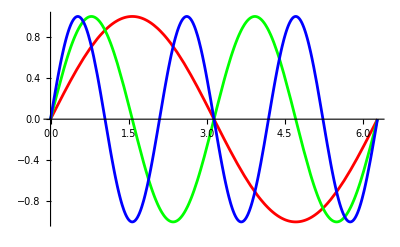

```mathematica
Plot[{Sin[x], Sin[2x], Sin[3x]}, {x, 0, 2Pi}, PlotStyle->{Red, Green, Blue}]
```

# Gráfica del seno con rango (0-3Pi), con color Rojo

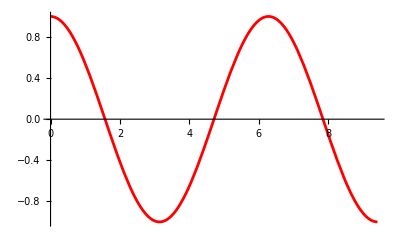

```mathematica
Plot[Cos[x], {x, 0, 3Pi}, PlotStyle->Red]
```

# Gráfica de la secante con rango (0-3Pi), con color Verde

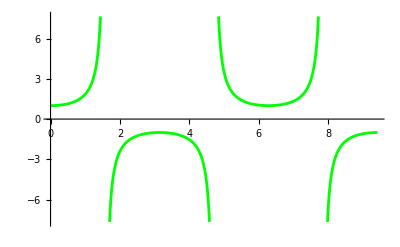

```mathematica
Plot[Sec[x], {x, 0, 3Pi}, PlotStyle->Green]
```

💎 Nota: También se puede usar TrigReduce o TrigFactor para otros tipos de simplificación según convenga..

## 6.2. Números complejos

📌 Explicación: Manipulación de números de la forma a+bi, incluyendo módulo (Abs), argumento (Arg), conjugado (Conjugate).

# Ingreso de un complejo con la paleta

```mathematica
ⅈ^2
```

-1

# Número complejo con parte real 3 y parte imaginaria 4

```mathematica
z1=3+4 ⅈ
```

3+4 ⅈ

# Número puramente imaginario, ingreso con teclado I (imaginario sin paleta)

```mathematica
z3=0+5 I
```

5 ⅈ

# Forma explícita de definir un número complejo

```mathematica
z4=Complex[1.5,-3.2]
```

1.5-3.2 ⅈ

# Número real (también válido como número complejo con parte imaginaria 0)

```mathematica
z5=6
```

6

# Parte real

```mathematica
Re[-2I]
```

0

# Parte imaginaria

```mathematica
Im[3-9I]
```

-9

# Módulo:sqrt[(Re^2+Im^2)

```mathematica
Abs[2-I]
```

√5

# Argumento o ángulo

```mathematica
Arg[7-3I]
```

-ArcTan[3/7]

# Conjugado:3-4 I

```mathematica
Conjugate[3+4I]
```

3-4 ⅈ

# Gráfica muestra de complejos en el plano

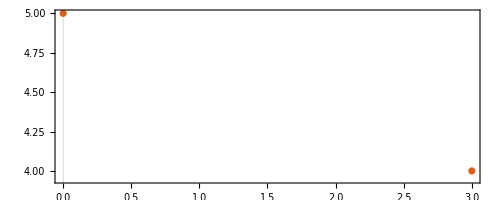

```mathematica
ComplexListPlot[{z1,z2,z3}, PlotTheme->"Scientific"]
```

💎 Nota: Se pueden graficar en el plano complejo con ComplexPlot, o usar Re/Im para separar partes reales e imaginarias.

## 6.3. Logaritmos

📌 Explicación: Uso de Log[x] para logaritmo natural. Se puede cambiar la base con Log[b, x].

# Evalúa Log[2] con una precisión de 20 dígitos decimales

```mathematica
N[Log[2], 20]
```

0.69314718055994530942

# Evalúa Log[π] con una precisión de 85 dígitos decimales

```mathematica
N[π, 85]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628

# Evalúa logaritmo en base 10 de 11 con precisión numérica

```mathematica
N[Log[10, 11]]
```

1.04139

# Evalúa el resultado anterior

```mathematica
Log[%]
```

0.0405589

# Calcula logaritmo de E en base π

```mathematica
Log[π, ⅇ]
```

1/Log[π]

# Gráfico función Logarítmica

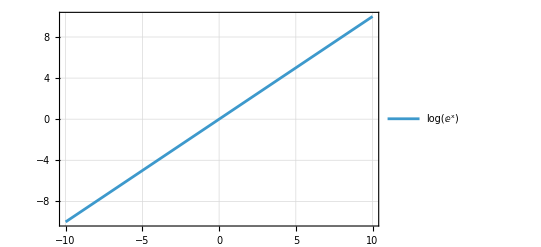

```mathematica
Plot[Log[E^x], {x, -10, 10}, PlotTheme->"Detailed"]
```

💎 Nota: Recordar que Log[0] y Log[negativo] no están definidos para números reales

## 6.4. Exponenciales

📌 Explicación: Uso de Exp[x] para ⅇ^x, con capacidad de manipular exponenciales complejos o combinarlos con otras funciones.

# Calcula la constante e (base de los logaritmos naturales)

```mathematica
Exp[1]
```

ⅇ

# Eleva la constante e a la potencia 6

```mathematica
E^6
```

ⅇ^6

# Evalúa e elevado al infinito (resultado infinito)

```mathematica
Exp[Infinity]
```

∞

# Evalúa e elevado a menos infinito (resultado cero)

```mathematica
E^(-∞)
```

0

# Gráfico función Exponencial

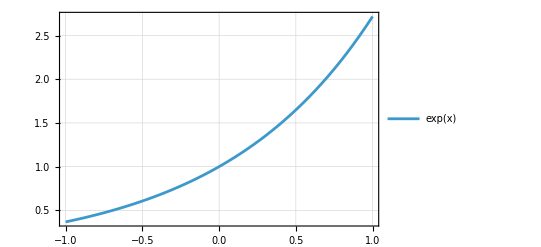

```mathematica
Plot[Exp[x], {x, -1, 1}, PlotTheme->"Detailed"]
```

💎 Nota: E^x también es válido, pero Exp[x] es más claro para composición.

## 6.5. Series

📌 Explicación: Series[f[x], {x, a, n}] da la expansión de Taylor en torno a 𝑥 = 𝑎; si 𝑎 = 0, se llama Maclaurin.

# Calcula la serie de Taylor de Exp[x] alrededor de x = -10 hasta el término de orden 10

```mathematica
Series[Exp[x], {x, -10, 10}]
```

1/ⅇ^10+(x+10)/ⅇ^10+(x+10)^2/(2 ⅇ^10)+(x+10)^3/(6 ⅇ^10)+(x+10)^4/(24 ⅇ^10)+(x+10)^5/(120 ⅇ^10)+(x+10)^6/(720 ⅇ^10)+(x+10)^7/(5040 ⅇ^10)+(x+10)^8/(40320 ⅇ^10)+(x+10)^9/(362880 ⅇ^10)+(x+10)^10/(3628800 ⅇ^10)+O[x+10]^11

# Convierte la serie en una expresión polinómica normal (sin los símbolos de serie)

```mathematica
Normal[%]
```

1/ⅇ^10+(10+x)/ⅇ^10+(10+x)^2/(2 ⅇ^10)+(10+x)^3/(6 ⅇ^10)+(10+x)^4/(24 ⅇ^10)+(10+x)^5/(120 ⅇ^10)+(10+x)^6/(720 ⅇ^10)+(10+x)^7/(5040 ⅇ^10)+(10+x)^8/(40320 ⅇ^10)+(10+x)^9/(362880 ⅇ^10)+(10+x)^10/(3628800 ⅇ^10)

# Serie de Potencia manual

```mathematica
Sum[a[n] (x-x0)^n,{n,0,Infinity}]
```

∑_(n=0)^∞ (x-x0)^n a[n]

# Define una función por tramos tipo onda cuadrada 
# Calcula la serie de Fourier hasta el 5to término 
# Se usa la variable x como independiente 
# La función es impar → solo aparecen senos 
# El resultado es una suma trigonométrica que aproxima la función periódica

```mathematica
FourierSeries[Piecewise[{{1,0<x<Pi},{-1,-Pi<x<0}}],x,5]
```

(2 ⅈ ⅇ^(-ⅈ x))/π-(2 ⅈ ⅇ^(ⅈ x))/π+(2 ⅈ ⅇ^(-3 ⅈ x))/(3 π)-(2 ⅈ ⅇ^(3 ⅈ x))/(3 π)+(2 ⅈ ⅇ^(-5 ⅈ x))/(5 π)-(2 ⅈ ⅇ^(5 ⅈ x))/(5 π)

# f[x_] define la función tipo onda cuadrada con valores -1 y 1 *)
# fs guarda la serie de Fourier truncada al quinto término *)
# Plot dibuja tanto la función original como su aproximación por Fourier *)
# PlotStyle usa línea gruesa para la original y línea discontinua para la serie *)
# PlotLegends muestra etiquetas para cada curva *)
# PlotLabel da un título explicativo al gráfico *)
# AxesLabel nombra los ejes con notación matemática *)

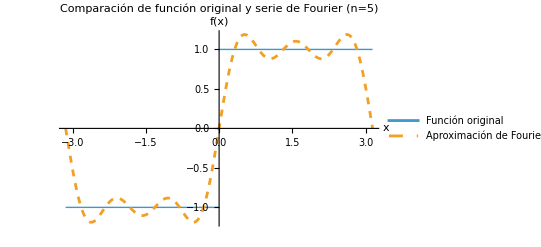

```mathematica
f[x_]:=Piecewise[{{1,0<x<Pi},{-1,-Pi<x<0}}]
fs=FourierSeries[f[x],x,5];

Plot[{f[x],fs},{x,-Pi,Pi},PlotStyle->{Thick,Dashed},PlotLegends->{"Función original","Aproximación de Fourier"},PlotLabel->"Comparación de función original y serie de Fourier (n=5)",AxesLabel->{HoldForm[x],HoldForm[f[x]]}]
```

💎 Nota:

Piecewise permite definir funciones por tramos (muy útil en Fourier).

Las series de Fourier aproximan funciones periódicas usando sumas de senos y cosenos.

Esta función es impar, por eso la serie contiene solo senos.

El parámetro 5 determina la cantidad de términos incluidos (mayor n = mejor aproximación).

# Grafica las aproximaciones polinómicas de la serie de Taylor de Cos[x] alrededor de 0
# desde el término de orden 1 hasta 20, para x en el intervalo [0, 3 Pi]

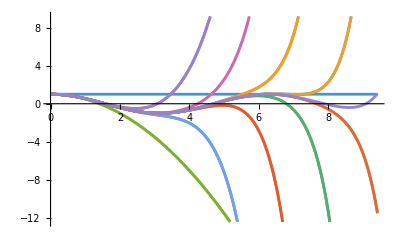

```mathematica
Plot[Evaluate[Table[Normal[Series[Cos[x],{x, 0, n}]], {n, 20}]], {x, 0, 3Pi}]
```

💎 Nota:

Normal elimina el término 𝑂[𝑥]𝑛 para obtener la expresión truncada.

También se pueden construir series de potencias más generales.

Series útiles para aproximaciones locales o resolver ecuaciones diferenciales.

## 6.6. Límites

📌 Explicación: Limit[f[x], x -> a] evalúa el comportamiento de una función cerca de un punto.

# Calcula el límite de Sin[x]/x cuando x tiende a 0

```mathematica
Limit[Sin[x]/x, x->0]
```

1

# Calcula el límite de Tan[x]/Sin[x] cuando x tiende a 0

```mathematica
Limit[Tan[x]/Sin[x], x -> 0]
```

1

# Calcula el límite de la raíz cuadrada de (2 + 5x - 3x^3)/(x^2 - 1) cuando x tiende a 3

```mathematica
Limit[Sqrt[(2+5x-3x^3)/(x^2-1)], x ->3]
```

2 ⅈ √2

# Calcula el límite de (1 + Sinh[x])/Exp[x] cuando x tiende a infinito positivo

```mathematica
Limit[(1+Sinh[x])/(Exp[x]), x ->Infinity]
```

1/2

# Calcula el límite de (1 + Sinh[x])/Exp[x] cuando x tiende a infinito negativo

```mathematica
Limit[(1+Sinh[x])/(Exp[x]), x ->- Infinity]
```

-∞

# Calcula el límite de (x^2 - 3x + 2)(x - 3) cuando x tiende a -3

```mathematica
Limit[(x^2-3x+2)(x-3), x ->- 3]
```

-120

# Evalúa f en x = -3

```mathematica
f[x_]=(x^2-3x+2)(x-3)
f[-3]
```

(-3+x) (2-3 x+x^2)

-120

```mathematica
Limit[5/(x+3)^3, x ->- 3]
```

Indeterminate

# Grafica la función 5/(x + 3)^3 en el intervalo [-6, 6]

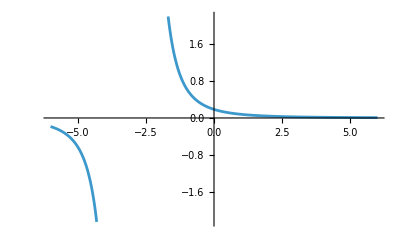

```mathematica
Plot[5/(x+3)^3 ,{x ,-6, 6}]
```

# Grafica (1 + Sinh[x])/Exp[x] y la constante 1/2 en [0, 10], con estilo de línea dif

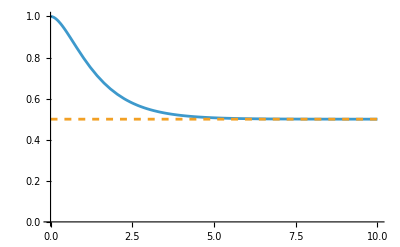

```mathematica
Plot[{(1+Sinh[x])/Exp[x], 1/2}, {x,0, 10}, PlotStyle->{Automatic, Dashed}, PlotRange->{0, 1}]
```

```mathematica
Limit[1/(x-2^2), x ->2]
```

-1/2

```mathematica
Limit[1/x, x ->Infinity]
```

0

# Grafica 1/(x - 2)^2 en el intervalo [1, 3]

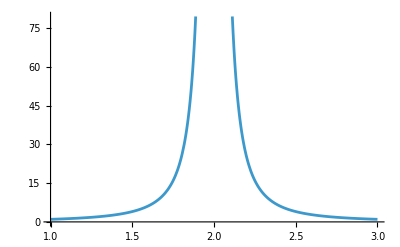

```mathematica
Plot[1/(x-2)^2, {x, 1, 3}]
```

```mathematica
Limit[Sin[2x]/Sin[x], x ->Pi]
```

-2

💎 Nota: puedes usar Direction -> “x → a⁺” o “x → a⁻)” para límites laterales. Útil para detectar discontinuidades.

# Límite lateral derecho: x → 1^+

```mathematica
Limit[1/(x-1),x->1,Direction->1]
```

-∞

# Límite lateral izquierdo: x → 1^-

```mathematica
Limit[1/(x-1),x->1,Direction->-1]
```

∞

## 6.7. Funciones

📌 Explicación: Definición de funciones con f[x_] := .... Permite reutilizar cálculos o construir modelos matemáticos.

# Definición de una función

```mathematica
f[x_]=x^2
```

x^2

# Gráfica de la función x&2 de 0 a infinito

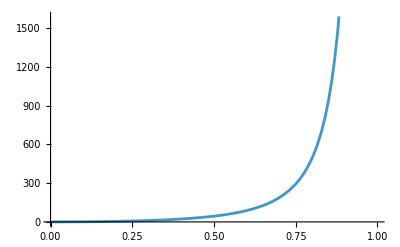

```mathematica
Plot[f[x], {x, 0, Infinity}]
```

# Definición de una función

```mathematica
f[x_]=(x^2 -3x +2)(x-3)
```

(-3+x) (2-3 x+x^2)

# Definir función mejora claridad y permite reutilizarla en cálculos posteriores
# Facilita operaciones simbólicas como FourierSeries al tener función explícita
# También se puede usar expresión directa, pero definir función es más ordenado y práctico

```mathematica
f[x_]:=x 
FourierSeries[f[x],x,5]
```

ⅈ ⅇ^(-ⅈ x)-ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-2 ⅈ x)+1/2 ⅈ ⅇ^(2 ⅈ x)+1/3 ⅈ ⅇ^(-3 ⅈ x)-1/3 ⅈ ⅇ^(3 ⅈ x)-1/4 ⅈ ⅇ^(-4 ⅈ x)+1/4 ⅈ ⅇ^(4 ⅈ x)+1/5 ⅈ ⅇ^(-5 ⅈ x)-1/5 ⅈ ⅇ^(5 ⅈ x)

💎 Nota:

FourierSeries solo puede aplicarse a funciones matemáticas continuas o definidas por tramos en un intervalo.

No opera sobre listas de números ni sobre expresiones que no dependan de una variable.

# Reemplaza x por 3 en la expresión x^2

```mathematica
x^2/. x->3
```

9

# Reemplazo múltiple (más de una variable)

```mathematica
x^2+y/. {x->2,y->5}
```

9

# Aplica el reemplazo x → 4 a cada elemento de la lista

```mathematica
{x^2,x+1,x-3}/. x->4
```

{16,5,1}

# Sustituye x por t y y por Sin[t] en la expresión

```mathematica
a x^2+b y/. {x->t,y->Sin[t]}
```

a t^2+b Sin[t]

# Aplica el reemplazo x → 3 dentro del resultado de f[x]

```mathematica
f[x_]:=x^2+1
f[x]/. x->3
```

10

💎 Nota:

/. se llama ReplaceAll.

Siempre se usa con la regla variable -> valor.

Se puede usar con listas de reglas {x -> ..., y -> ...} para múltiples reemplazos.

Funciona con expresiones simbólicas o numéricas.

```mathematica
f[t_] = x^2+5x-3
```

-3+5 x+x^2

# Definición de una función

```mathematica
f[x_] = Sin[x]
```

Sin[x]

# Evaluar la función f en el punto x = Pi

```mathematica
f[Pi]
```

0

💎 Nota: se pueden definir funciones de varias variables o incluso condicionales.

## 6.8. Derivadas

📌 Explicación: D[f[x], x] calcula la derivada simbólica; N[D[...]] evalúa el valor numérico.

# D es una predefinida, no podemos dar un valor

```mathematica
D = 9
```

Set::wrsym: Symbol D is Protected.

9

# Forma clásica de derivada de una exponencial

```mathematica
D[x^n, x]
```

n x^(-1+n)

# Calcula la derivada del coseno, evaluada en x

```mathematica
D[Cos[x], x]
```

-Sin[x]

# Calcula la derivada del valor anterior, evaluada en x

```mathematica
D[%, x]
```

-Cos[x]

```mathematica
D[ArcTan[x], x]
```

1/(1+x^2)

# Calcula la derivada evaluada en y

```mathematica
D[x y^2, y]
```

2 x y

# Calcula la derivada evaluada en x

```mathematica
D[x y^2,x]
```

y^2

# Derivada de una suma

```mathematica
D[u[x]+v[x], x]
```

u'[x]+v'[x]

# Derivada de una división

```mathematica
D[u[x]/v[x], x]
```

u'[x]/v[x]-(u[x] v'[x])/v[x]^2

# Derivación por definición

```mathematica
Limit[(t(x+h)-t(x))/h, h ->0]
```

t

💎 Nota: también se puede usar la notación de Lagrange con ‘, por ejemplo, f’[x], o f’’[x].

## 6.9. Integrales

📌 Explicación: Integrate[f[x], {x, a, b}]  y Integrate[f[x], x] calcula integrales definidas e indefinidas.

# Calcula la integral a través de la paleta

```mathematica
∫xⅆx
```

x^2/2

# Integral definida  de 0 a 1

```mathematica
∫_0^1 x^2/2 ⅆx
```

1/6

# Integral definida  de 1 a 0

```mathematica
∫_1^0 x^2/2 ⅆx
```

-1/6

# Definiendo una función
# Derivada con notación de Lagrange
# Integral por teorema fundamental del cálculo

```mathematica
h[t_]  = t^2
```

t^2

```mathematica
h'[t]
```

2 t

```mathematica
∫_a^b h'[t]ⅆt
```

2 (-a^2/2+b^2/2)

```mathematica
∫Sin[t]ⅆt
```

-Cos[t]

```mathematica
∫Sinh[t]ⅆt
```

Cosh[t]

```mathematica
∫Sec[x]ⅆx
```

ArcCoth[Sin[x]]

```mathematica
∫Csc[x]ⅆx
```

-ArcTanh[Cos[x]]

```mathematica
∫Cot[x]ⅆx
```

Log[Sin[x]]

# Representación simbólica de la integral indefinida de √(a + b t + c t.b2) con respecto a t

```mathematica
∫√(a+b t+c t^2)ⅆt
```

(√c (b+2 c t) √(a+t (b+c t))+(b^2-4 a c) ArcTanh[(√c t)/(√a-√(a+t (b+c t)))])/(4 c^(3/2))

# Integral indefinida de la función F respecto a su variable implícita

```mathematica
∫ⅆF
```

F

💎 Nota: si no es posible resolver simbólicamente, usar NIntegrate para una aproximación numérica.

## 6.10. Notación de Lagrange

📌 Explicación: f’[x], f’’[x], etc., representan derivadas de primer y segundo orden.

# Notación de Lagrange

```mathematica
g'[t]
```

g'[t]

# Definición de una función f[x] multiplicada por x^2

```mathematica
f[x_]*x^2
```

x^2 (1+x_^2)

# Definimos una función cuadrática

```mathematica
f[x_]=x^2
```

x^2

# Primera derivada

```mathematica
f'[x]
```

2 x

# Segunda derivada

```mathematica
f''[x]
```

2

💎 Nota: puede combinarse con Plot, Table o integrales para mostrar resultados analíticos y gráficos fácilmente.

## 6.11. Integración Numérica

📌 Explicación: Uso de NIntegrate para resolver integrales que no tienen solución simbólica exacta.

# Integral básica de una función trigonométrica sencilla

```mathematica
NIntegrate[Sin[x], {x, 0, π }]
```

2.

# Integral con función compuesta, más compleja que la anterior

```mathematica
NIntegrate[Sin[Sin[x]], {x ,0, π }]
```

1.78649

# Integral con función exponencial dentro del seno, más difícil de resolver analíticamente

```mathematica
NIntegrate[Sin[Exp[x]], {x ,0, π }]
```

0.644005

💎 Nota: muy útil cuando se trabaja con funciones definidas por datos o con funciones especiales.

## 6.12. Tablas

📌 Explicación: Creación de listas con Table, formateadas con TableForm, Grid o TableView.

# Tabla de pares ordenados (x, x.b2) para x desde 0 hasta 10

```mathematica
Tabla1= Table[{x, x^2}, {x ,0, 10}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

# Muestra en formato de tabla los pares ordenados (i, i×10) del 1 al 10

```mathematica
TableForm[Table[{i, i*10}, {i, 1, 10}]]
```

1 | 10
2 | 20
3 | 30
4 | 40
5 | 50
6 | 60
7 | 70
8 | 80
9 | 90
10 | 100

# Con pasos de 0.2

```mathematica
Table[{i, i*0.1}, {i, 1, 10, 0.2}]
```

{{1.,0.1},{1.2,0.12},{1.4,0.14},{1.6,0.16},{1.8,0.18},{2.,0.2},{2.2,0.22},{2.4,0.24},{2.6,0.26},{2.8,0.28},{3.,0.3},{3.2,0.32},{3.4,0.34},{3.6,0.36},{3.8,0.38},{4.,0.4},{4.2,0.42},{4.4,0.44},{4.6,0.46},{4.8,0.48},{5.,0.5},{5.2,0.52},{5.4,0.54},{5.6,0.56},{5.8,0.58},{6.,0.6},{6.2,0.62},{6.4,0.64},{6.6,0.66},{6.8,0.68},{7.,0.7},{7.2,0.72},{7.4,0.74},{7.6,0.76},{7.8,0.78},{8.,0.8},{8.2,0.82},{8.4,0.84},{8.6,0.86},{8.8,0.88},{9.,0.9},{9.2,0.92},{9.4,0.94},{9.6,0.96},{9.8,0.98},{10.,1.}}

# 10 primeros números primos

```mathematica
Table[Prime[i], {i, 1, 10}]
```

{2,3,5,7,11,13,17,19,23,29}

# Muestra en una cuadrícula los primeros 10 números naturales junto con su número primo correspondiente

```mathematica
Grid[Table[{i, Prime[i]}, {i, 10}]]
```

1 | 2
2 | 3
3 | 5
4 | 7
5 | 11
6 | 13
7 | 17
8 | 19
9 | 23
10 | 29

@ Números impares primos

```mathematica
TableForm[Table[{2n+1, 2n}, {n, 0, 10}]]
```

1 | 0
3 | 2
5 | 4
7 | 6
9 | 8
11 | 10
13 | 12
15 | 14
17 | 16
19 | 18
21 | 20

# Serie de 0.1 hasta 1 con paso de 0.1

```mathematica
Table[0.1n, {n, 1, 10}]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

# Serie de 0.1 (otra forma)

```mathematica
N[Table[n/10, {n, 0, 10}]]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

# Números pares

```mathematica
Table[2n, {n, 1, 10}]
```

{2,4,6,8,10,12,14,16,18,20}

# Serie de 0.1 hasta 1 con paso de 0.1

```mathematica
TableForm[Table[{i, i*10}, {i, 1, 10}]]
```

1 | 10
2 | 20
3 | 30
4 | 40
5 | 50
6 | 60
7 | 70
8 | 80
9 | 90
10 | 100

# primera columna números pares y otra columna números impares

```mathematica
tableX= Table[{2n+1, 2n}, {n, 0, 10}]
```

{{1,0},{3,2},{5,4},{7,6},{9,8},{11,10},{13,12},{15,14},{17,16},{19,18},{21,20}}

# Genera una tabla con los valores de x y sus funciones trigonométricas (Coseno, Seno, Tangente) evaluadas numéricamente de x = 0 a 100

```mathematica
Table[{x, N[Cos[x]], N[Sin[x]], N[Tan[x]]}, {x, 0, 100}]
```

{{0,1.,0.,0.},{1,0.540302,0.841471,1.55741},{2,-0.416147,0.909297,-2.18504},{3,-0.989992,0.14112,-0.142547},{4,-0.653644,-0.756802,1.15782},{5,0.283662,-0.958924,-3.38052},{6,0.96017,-0.279415,-0.291006},{7,0.753902,0.656987,0.871448},{8,-0.1455,0.989358,-6.79971},{9,-0.91113,0.412118,-0.452316},{10,-0.839072,-0.544021,0.648361},{11,0.0044257,-0.99999,-225.951},{12,0.843854,-0.536573,-0.63586},{13,0.907447,0.420167,0.463021},{14,0.136737,0.990607,7.24461},{15,-0.759688,0.650288,-0.855993},{16,-0.957659,-0.287903,0.300632},{17,-0.275163,-0.961397,3.49392},{18,0.660317,-0.750987,-1.13731},{19,0.988705,0.149877,0.151589},{20,0.408082,0.912945,2.23716},{21,-0.547729,0.836656,-1.5275},{22,-0.999961,-0.00885131,0.00885166},{23,-0.532833,-0.84622,1.58815},{24,0.424179,-0.905578,-2.1349},{25,0.991203,-0.132352,-0.133526},{26,0.646919,0.762558,1.17875},{27,-0.292139,0.956376,-3.2737},{28,-0.962606,0.270906,-0.28143},{29,-0.748058,-0.663634,0.887143},{30,0.154251,-0.988032,-6.40533},{31,0.914742,-0.404038,-0.441696},{32,0.834223,0.551427,0.661006},{33,-0.0132767,0.999912,-75.313},{34,-0.84857,0.529083,-0.623499},{35,-0.903692,-0.428183,0.473815},{36,-0.127964,-0.991779,7.75047},{37,0.765414,-0.643538,-0.840771},{38,0.955074,0.296369,0.31031},{39,0.266643,0.963795,3.61455},{40,-0.666938,0.745113,-1.11721},{41,-0.987339,-0.158623,0.160657},{42,-0.399985,-0.916522,2.29139},{43,0.555113,-0.831775,-1.49839},{44,0.999843,0.0177019,0.0177047},{45,0.525322,0.850904,1.61978},{46,-0.432178,0.901788,-2.08661},{47,-0.992335,0.123573,-0.124528},{48,-0.640144,-0.768255,1.20013},{49,0.300593,-0.953753,-3.17291},{50,0.964966,-0.262375,-0.271901},{51,0.742154,0.670229,0.903086},{52,-0.162991,0.986628,-6.05327},{53,-0.918283,0.395925,-0.431158},{54,-0.82931,-0.558789,0.6738},{55,0.0221268,-0.999755,-45.1831},{56,0.85322,-0.521551,-0.611274},{57,0.899867,0.436165,0.484699},{58,0.11918,0.992873,8.33086},{59,-0.77108,0.636738,-0.825774},{60,-0.952413,-0.304811,0.32004},{61,-0.258102,-0.966118,3.74317},{62,0.673507,-0.739181,-1.09751},{63,0.985897,0.167356,0.16975},{64,0.391857,0.920026,2.34786},{65,-0.562454,0.826829,-1.47004},{66,-0.999647,-0.0265512,0.0265605},{67,-0.51777,-0.85552,1.65232},{68,0.440143,-0.897928,-2.04008},{69,0.99339,-0.114785,-0.115549},{70,0.633319,0.773891,1.22196},{71,-0.309023,0.951055,-3.07762},{72,-0.967251,0.253823,-0.262417},{73,-0.736193,-0.676772,0.919286},{74,0.171717,-0.985146,-5.73702},{75,0.921751,-0.387782,-0.420701},{76,0.824331,0.566108,0.686748},{77,-0.030975,0.99952,-32.2686},{78,-0.857803,0.513978,-0.59918},{79,-0.895971,-0.444113,0.495678},{80,-0.110387,-0.993889,9.00365},{81,0.776686,-0.629888,-0.810994},{82,0.949678,0.313229,0.329826},{83,0.24954,0.968364,3.8806},{84,-0.680023,0.73319,-1.07818},{85,-0.984377,-0.176076,0.17887},{86,-0.383698,-0.923458,2.40673},{87,0.56975,-0.821818,-1.44242},{88,0.999373,0.0353983,0.0354205},{89,0.510177,0.860069,1.68583},{90,-0.448074,0.893997,-1.9952},{91,-0.994367,0.105988,-0.106588},{92,-0.626444,-0.779466,1.24427},{93,0.317429,-0.948282,-2.98739},{94,0.969459,-0.245252,-0.252978},{95,0.730174,0.683262,0.935752},{96,-0.18043,0.983588,-5.45134},{97,-0.925148,0.379608,-0.410321},{98,-0.819288,-0.573382,0.699854},{99,0.0398209,-0.999207,-25.0925},{100,0.862319,-0.506366,-0.587214}}

# Tabla de valores de x y Coseno evaluado numericamente
# Prepend agrega encabezados a la tabla
# TableView muestra la tabla en formato visual con marco
# Style cambia el tamaño de fuente para mejor lectura

```mathematica
Style[TableView[Prepend[Table[{x,N[Cos[x]]},{x,0,10}],{"x","Cos(x)"}],Alignment->Center,AppearanceElements->{"Frame"}],FontSize->14]
```

xCos(x)01.10.54030230586813982-0.41614683654714243-0.98999249660044544-0.653643620863611950.2836621854632262560.96017028665036670.75390225434330468-0.145500033808613549-0.911130261884676910-0.8390715290764524

💎 Nota: se pueden usar encabezados personalizados y aplicar estilos con Style, FontSize, Alignment, etc..

## 6.13. Gráfica de Tablas

📌 Explicación: Uso de ListPlot, ListLinePlot o BarChart para representar datos tabulados.

```mathematica
Tabla1= Table[{x, x^2}, {x ,0, 10}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

# Grafica los puntos de la lista Tabla1 en un diagrama de dispersión (ListPlot)

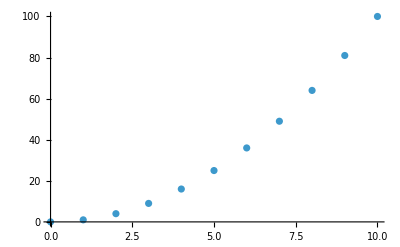

```mathematica
ListPlot[Tabla1]
```

# Grafica una línea conectando los puntos de la lista Tabla1 (ListLinePlot)

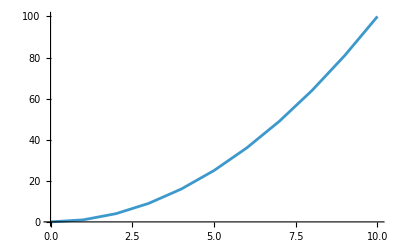

```mathematica
ListLinePlot[Tabla1]
```

# Grafica una línea conectando los puntos de Tabla1  
# Filling -> Axis: rellena el área bajo la curva hasta el eje horizontal

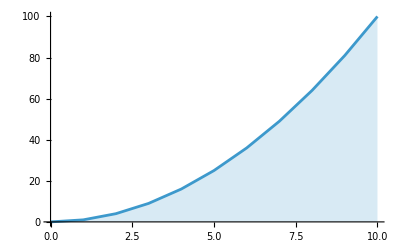

```mathematica
ListLinePlot[Tabla1, Filling->Axis]
```

🎯 Reto en clase — Gráfica con listas
Graficar múltiples puntos rojos de la lista1 y una línea azul que una los mismos.

```mathematica
?ListLinePlot
```

```mathematica
?PlotStyle
```

```mathematica
?Epilog
```

# ListLinePlot → crea una gráfica de líneas conectando puntos de datos.
# Tabla1 → contiene los datos a graficar (debe ser una lista de pares {x, y}).
# Filling -> Axis → sombrea el área entre la curva y el eje horizontal.
# PlotStyle -> {Blue, Thick} → define el color azul y grosor de la línea.
# Epilog -> {Red, PointSize[0.015], Point[Tabla1]} → sobrepone los puntos de datos en rojo encima de la línea para resaltarlos.

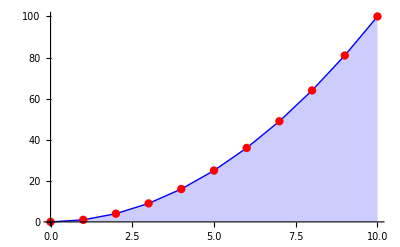

```mathematica
ListLinePlot[Tabla1,Filling->Axis,PlotStyle->{Blue,Thick},Epilog->{Red,PointSize[0.015],Point[Tabla1]}]
```

# ListPlot → crea una gráfica de puntos sin conectar líneas.
# Tabla1 → lista de pares {x, y} que se van a graficar.
# PlotStyle -> {Blue, PointSize[0.015]} → define el color azul para los elementos y el tamaño de los puntos.
# Filling -> Axis → sombrea el área entre cada punto y el eje horizontal (efecto visual de “relleno”).
# PlotMarkers -> {Red, 10} → cambia el color de los marcadores (puntos) a rojo y el tamaño a 10.

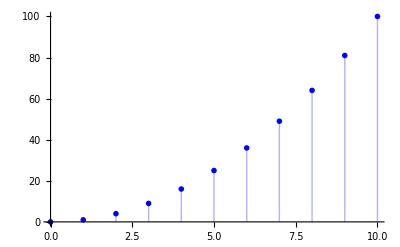

```mathematica
ListPlot[Tabla1,PlotStyle->{Blue,PointSize[0.015]},Filling->Axis,PlotMarkers->{Red,10} ]
```

🎯 Reto en clase — Funciones trigonométricas 
Graficar sombras bajo cada curva de diferentes colores y adicionalmente otra gráfica que sombreé la intersección de las mismas.

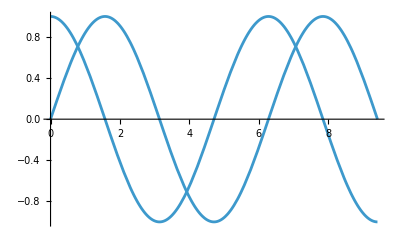

```mathematica
Show[Plot[Sin[x],{x,0,3 Pi}],Plot[Cos[x],{x,0,3 Pi}]]
```

#Plot -> Grafica Sin[x] y Cos[x] de 0 a 3π
#Filling -> Axis -> Sombreado desde cada curva hasta el eje x
#PlotStyle -> {Red, Blue} -> Color rojo para Sin[x], azul para Cos[x]
#PlotLegends -> “Expressions” -> Añade leyenda automática con funciones
#AxesLabel -> {x, f(x)} -> Etiquetas personalizadas en los ejes
#PlotLabel -> título con estilo (negrita, cursiva)
#LabelStyle -> Fuente Roboto Condensed para texto del gráfico

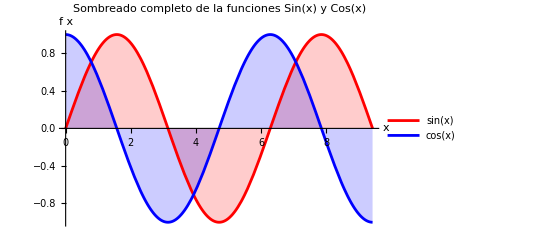

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,3 Pi},Filling->Axis,PlotStyle->{Red,Blue},PlotLegends->"Expressions", AxesLabel->{HoldForm[x],HoldForm[f(x)]}, PlotLabel->"Sombreado completo de la funciones Sin(x) y Cos(x)", LabelStyle->{FontFamily->"Roboto Condensed"}]
```

#Filling -> {1 -> {2}} -> Sombrea entre Sin[x] y Cos[x]
#FillingStyle -> LightOrange -> Color naranja claro para el relleno
#PlotStyle -> {Red, Blue} -> Color de las curvas
#PlotLegends -> “Expressions” -> Leyenda automática
#AxesLabel -> etiquetas personalizadas en los ejes
#PlotLabel -> título estilizado
#LabelStyle -> Fuente Roboto Condensed

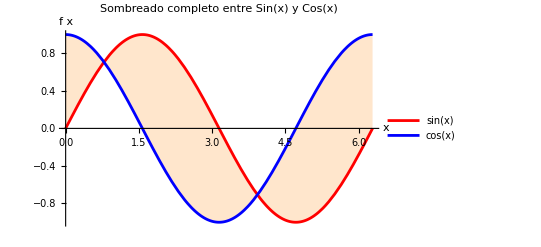

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},Filling->{1->{2}},FillingStyle->LightOrange,PlotStyle->{Red,Blue},PlotLegends->"Expressions",PlotLabel->"Sombreado completo entre Sin(x) y Cos(x)",AxesLabel->{HoldForm[x],HoldForm[f(x)]}, LabelStyle->{FontFamily->"Roboto Condensed"}]
```

#RegionFunction -> Function[{x,y}, Sin[x]>=Cos[x]] -> Sombrea solo donde Sin[x] ≥ Cos[x]
#FillingStyle -> LightGreen -> Color verde claro para relleno parcial
#Filling -> {1 -> {2}} -> Sombrea entre ambas funciones
#PlotStyle -> {Red, Blue} -> Colores de las curvas
#PlotLegends -> “Expressions” -> Leyenda automática
#AxesLabel -> etiquetas personalizadas
#PlotLabel -> título con estilo
#LabelStyle -> Fuente Roboto Condensed

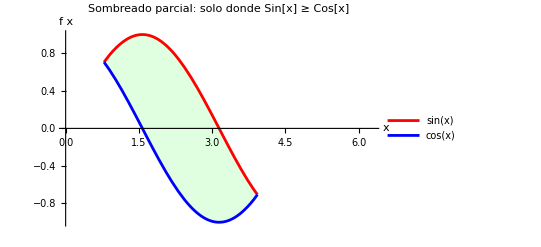

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},Filling->{1->{2}},FillingStyle->LightGreen,PlotStyle->{Red,Blue},PlotLegends->"Expressions",RegionFunction->Function[{x,y},Sin[x]>=Cos[x]],PlotLabel->"Sombreado parcial: solo donde Sin[x] ≥ Cos[x]",AxesLabel->{HoldForm[x],HoldForm[f(x)]}, LabelStyle->{FontFamily->"Roboto Condensed"}]
```

💎 Nota:

Para sombrear la región entre dos funciones, se usa Filling -> {1 -> 2}, donde 1 y 2 indican las curvas a conectar con relleno.

Cuando se sombrea solo la intersección, es útil RegionFunction para limitar la zona según condiciones entre funciones (ejemplo: Sin[x] >= Cos[x]).

# Grafica la función seno desde 0 hasta 10π  
# Ticks -> personaliza las marcas del eje x en múltiplos de π  
# AxesLabel -> etiquetas de los ejes (“x”, “Sin(x)”)

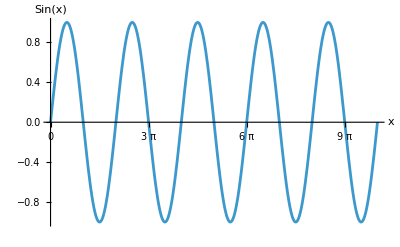

```mathematica
Plot[Sin[x], {x, 0, 10Pi}, Ticks->{Table[{n Pi, n Pi}, {n, 0, 10}], Automatic}, AxesLabel->{"x", "Sin(x)"}]
```

# Gráfica Tabla de los números pares e impares

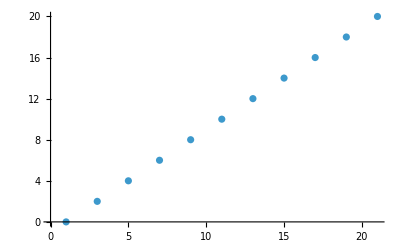

```mathematica
ListPlot[tableX]
```

# Ambas funciones se grafican en el mismo rango, por eso se cruzan donde tienen el mismo valor

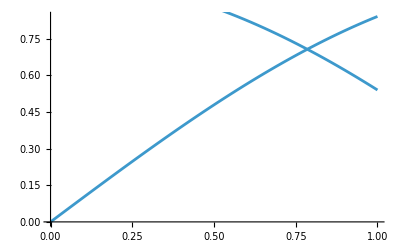

```mathematica
Show[Plot[Sin[x], {x, 0, 1}], Plot[Cos[x], {x, 0, 1}]]
```

💎 Nota: Agregar PlotMarkers, Filling, Epilog y leyendas mejora mucho la presentación visual.

## 7. Clase 5 — Visualización matemática interactiva

📆 2025/10/01

⚡ Introducción:

Lorem Ipsum

📘 Objetivos de la clase:

## 7.1 Gráficas Bidimensionales (2D)

📌 Explicación:

# Dibuja un círculo con centro en (0, 0) y radio 1 por defecto



```mathematica
Graphics[{Circle[]}]
```

# Dibuja un círculo en (0, 0) con radio 1 y lo colorea de púrpura

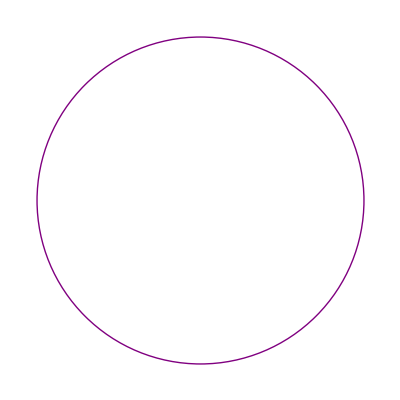

```mathematica
Graphics[Style[Circle[], Purple]]
```

# Dibuja un círculo en (0, 0) con radio 1 y lo colorea de verde

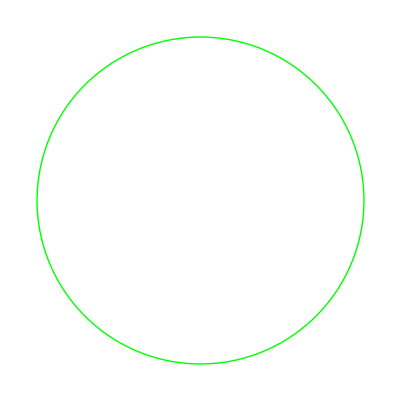

```mathematica
Graphics[Style[Circle[], Green]]
```

# Dibuja un círculo con centro en (1, 1) y radio 0.5

```mathematica
Graphics[Circle[{1, 1}, 0.5]]
```

-Graphics-

# Dibuja un disco sólido con centro en (0, 0) y radio 1, de color rojo



```mathematica
Graphics[Style[Disk[], Red]]
```

# Dibuja un disco naranja claro con centro en (0, 0) y radio 1, y encima un círculo azul en el mismo lugar

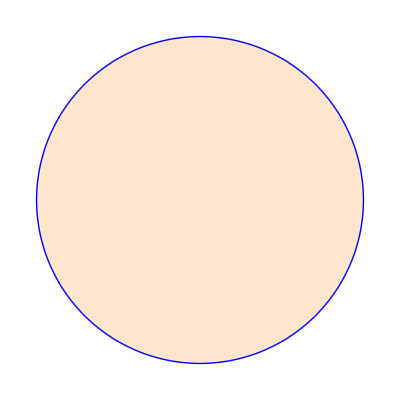

```mathematica
Graphics[{LightOrange, Disk[], Blue, Circle[]}]
```

# Dibuja un polígono regular de 7 lados centrado en (0, 0) y lo colorea de rosa

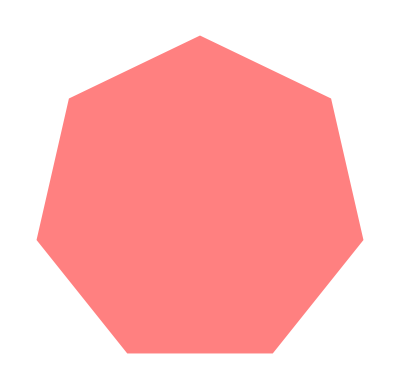

```mathematica
Graphics[Style[RegularPolygon[7],Pink]]
```

# Dibuja un polígono regular de 4 lados (cuadrado) centrado en (0, 0) y lo colorea de verde claro

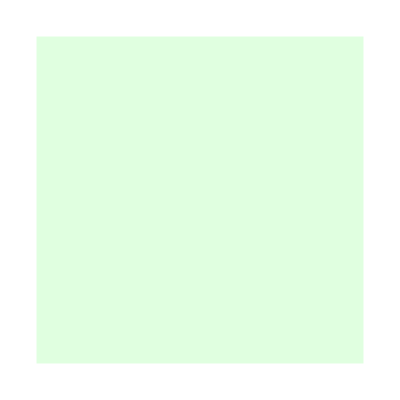

```mathematica
Graphics[Style[RegularPolygon[4],LightGreen]]
```

# Dibuja un polígono regular de 12 lados centrado en (0, 0) y lo colorea de magenta

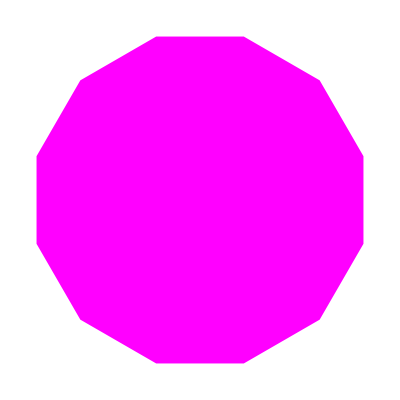

```mathematica
Graphics[Style[RegularPolygon[12],Magenta]]
```

# Genera gráficos de polígonos regulares con lados desde 5 hasta 10, uno para cada valor de n

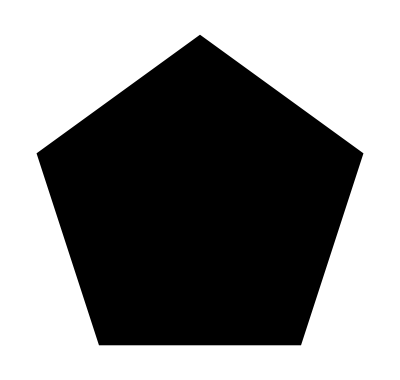
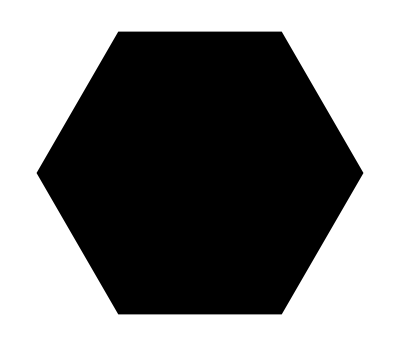
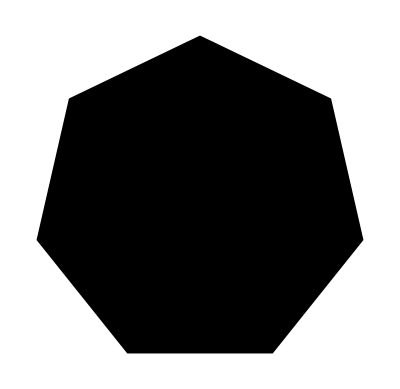
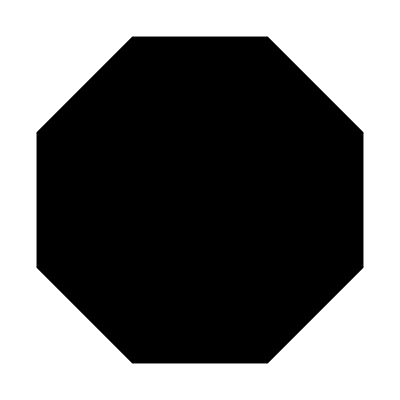
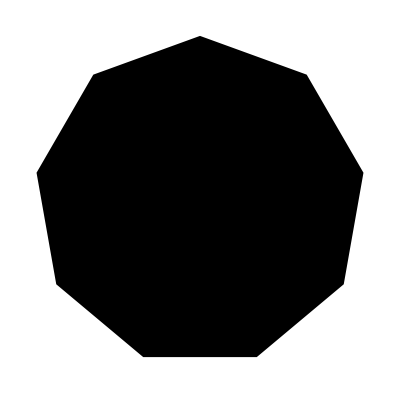
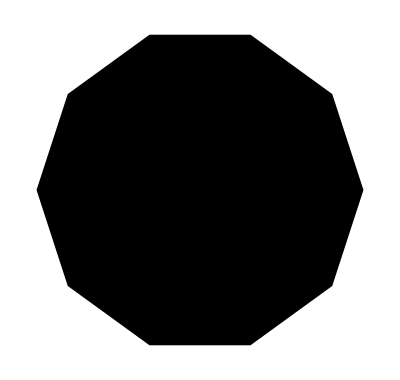

```mathematica
Table[Graphics[RegularPolygon[n]],{n,5,10}]
```

# Genera gráficos de polígonos regulares con lados desde 5 hasta 10, uno para cada valor de n en color rosado

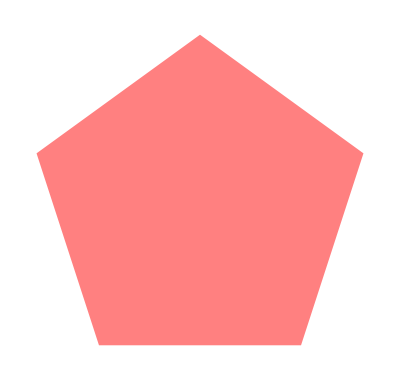
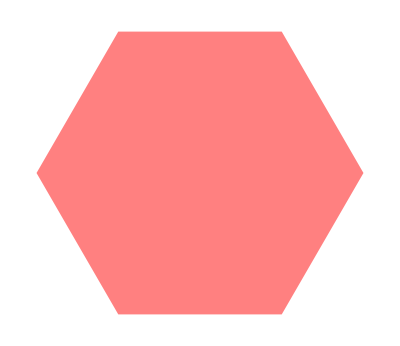
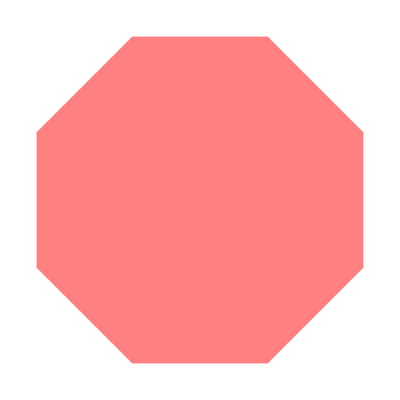
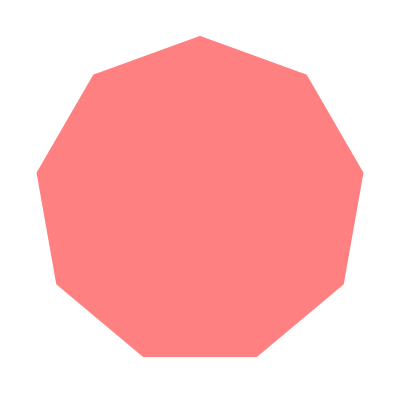
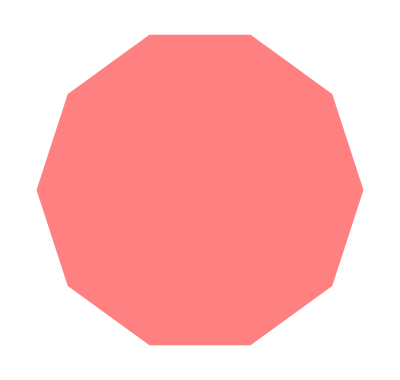
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Style[RegularPolygon[n], Pink]],{n,5,10}]
```

## 7.2 Gráficas Tridimensionales (3D)

📌 Explicación:

# Dibuja una esfera en 3D con centro en (0, 0, 0) y radio 1 por defecto

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

# Dibuja una esfera 3D roja con centro en (0, 0, 0) y radio 1 por defecto

```mathematica
Graphics3D[Style[Sphere[],Red]]
```

-Graphics3D-

# Dibuja un cono y un cilindro 3D, ambos con dimensiones y posiciones por defecto

```mathematica
{Graphics3D[Cone[]],Graphics3D[Cylinder[]]}
```

{-Graphics3D-,-Graphics3D-}

# Dibuja un cilindro 3D con base en (0, 0, 0), altura 1 y radio 1 por defecto

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

# Dibuja una esfera 3D amarilla con centro en (0,0,0) y radio 1, mostrando ejes con etiquetas x, y, z

```mathematica
Graphics3D[Style[Sphere[],Yellow],Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

# Dibuja un círculo con centro en (0, 0) y radio 1, mostrando ejes con etiquetas x y y

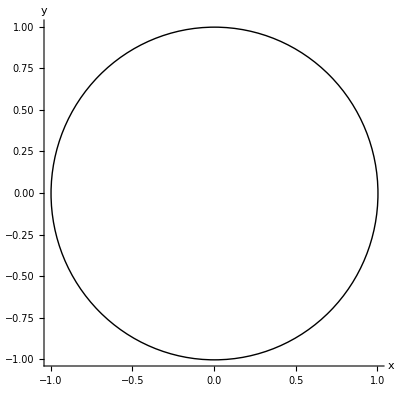

```mathematica
Graphics[Circle[], Axes->True, AxesLabel->{x,y}]
```

## 7.3 Manipuladores Interactivos

📌 Explicación:

# Crea un manipulador interactivo para evaluar x^n con n desde 1 hasta 10 en pasos de 2

```mathematica
Manipulate[x^n,{n,1,10,2}]
```

# Binomio de Newton

```mathematica
Manipulate[Expand[(a+b)^n],{n,1,10,1}]
```

Forma Binomial: (a+b)^n=∑_(k=0)^n (n/k)a^(n-k)b^k

# Sum[Binomial[n, k] a^(n - k) b^k, {k, 0, n}] genera directamente el desarrollo del binomio sin recurrir a Expand

💎 Nota:

Sum[Binomial[n, k] a^(n - k) b^k, {k, 0, n}] genera directamente el desarrollo del binomio sin recurrir a Expand.

Manipulate permite variar n dinámicamente de 1 a 10.

```mathematica
Manipulate[Sum[Binomial[n,k] a^(n-k) b^k,{k,0,n}],{n,1,10,1}]
```

# Muestra una tabla con {i^n, (2i)^n} para i de 1 a 10 y n de 1 a 10 en pasos de 2

```mathematica
Manipulate[Table[{i^n,(2 i)^n},{i,1,10}],{n,1,10,2}]
```

# Grafica Sin[x (1 + a x)] en x de 0 a 6, con a entre 0 y 10

```mathematica
Manipulate[Plot[Sin[x (1+a x)],{x,0,6}],{a,0,10}]
```

# Crea un manipulador interactivo para factorizar x^n + 1 con n de 10 a 100 en pasos de 1

```mathematica
Manipulate[Factor[x^n+1],{n,10,100,1}]
```

# Calcular el factorial de n con n de 1 a 50 en pasos de 1

```mathematica
Manipulate[n!,{n,1,50,1}]
```

# Crea un manipulador interactivo que genera una lista con n veces el color Orange, con n de 1 a 5

```mathematica
Manipulate[Table[Orange,n],{n,1,5,1}]
```

# Grafica Sin[a x + b] en x de 0 a 6, con a entre 1 y 4, y b entre 0 y 10

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],{a,1,4},{b,0,10}]
```

# Crea un manipulador interactivo que muestra en columna los valores n, n^2 y n^3 para n de 1 a 10

```mathematica
Manipulate[Column[{n,n^2,n^3}],{n,1,10,1}]
```

# Gráfico de barras 3D con alturas que dependen de a, variando a de 0 a 5

```mathematica
Manipulate[BarChart3D[{1,a,4,2*a,4,3*a,1}],{a,0,5}]
```

# Gráfico circular con sectores que dependen de a, variando a de 0 a 5

```mathematica
Manipulate[PieChart[{1,a,4,2*a,4,3*a,1}],{a,0,5}]
```

# Crea un manipulador interactivo que dibuja un polígono regular con n lados y color según Hue[h]; n varía de 3 a 20 y h de 0 a 1

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],Hue[h]]],{n,3,20,1},{h,0,1}]
```

💎 Nota: Espectro de Hue[h] (Hue, Saturation, Brightness), para h ∈ [0,1];  El cambio es suave y continuo. A medida que se mueve el deslizador de h, el color del polígono cambia por todo el arcoíris.

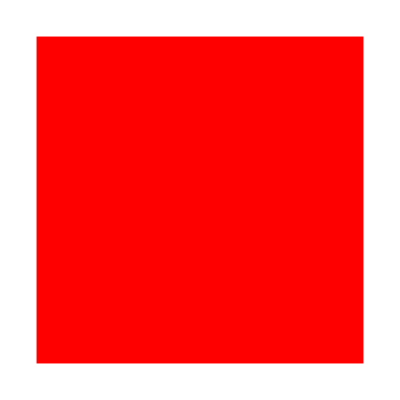
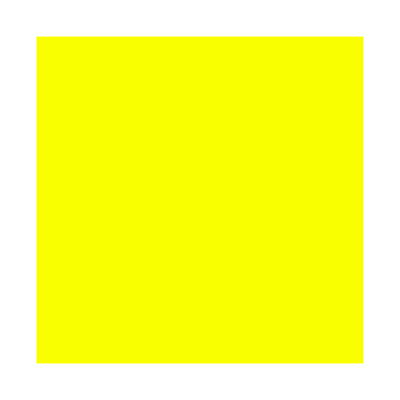
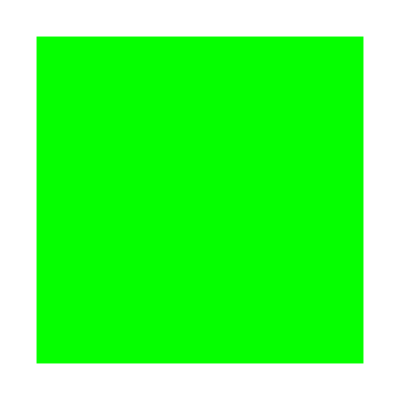
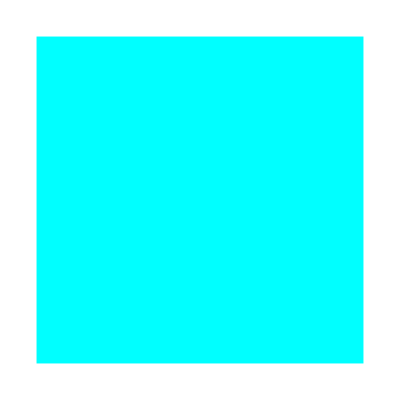
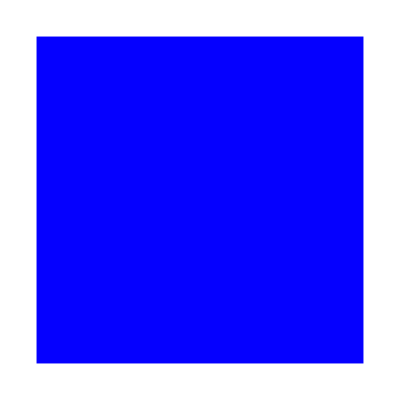
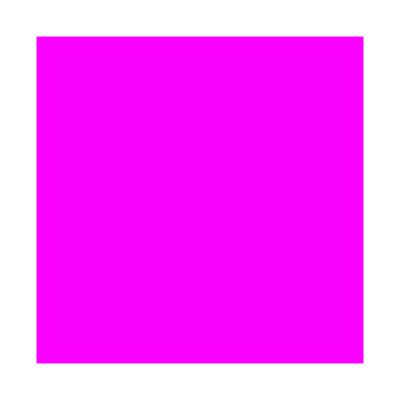
h | Color | Color Aproximado
0.00 | -Graphics- | Red
0.17 | -Graphics- | Yellow
0.33 | -Graphics- | Green
0.50 | -Graphics- | Cyan
0.67 | -Graphics- | Blue
0.83 | -Graphics- | Magenta
1.00 | -Graphics- | Red

```mathematica
Grid[Prepend[Table[{Style[NumberForm[h,{2,2}]],Style[Graphics[{Hue[h],Rectangle[]}]],Which[h==0.0,"Red",h<=0.17,"Yellow",h<=0.33,"Green",h<=0.5,"Cyan",h<=0.67,"Blue",h<=0.83,"Magenta",h<=1.0,"Red"]},{h,{0.0,0.17,0.33,0.5,0.67,0.83,1.0}}],{"h","Color","Color Aproximado"}],Frame->All]
```

# Intenta crear un gráfico circular con tres conjuntos de datos: {1,2,3}, {1,2}, y {1,2,3,5}, pero PieChart espera una lista plana de valores numéricos

```mathematica
PieChart[{Range[3],Range[2],{1,2,3,5}}]
```

-Graphics-

💎 Nota:

PieChart no acepta listas anidadas; se debe pasar una sola lista con números.

PieChart espera una lista plana de valores.

Pasar una lista anidada genera un error o un gráfico que no tiene sentido, porque intenta interpretar cada sublista como un sector (lo cual no está definido).

No hace un gráfico de dona ni agrupa sectores de forma esperada.

# Crea un gráfico circular con los valores {1, 2, 3, 1, 2, 1, 2, 3, 5} combinando todas las listas

```mathematica
PieChart[Flatten[{Range[3],Range[2],{1,2,3,5}}]]
```

-Graphics-

💎 Nota: La función Flatten toma una lista anidada y la convierte en una lista plana. Es decir, si tienes una lista que contiene otras listas dentro de ella, Flatten las “aplana” y las combina en una sola lista.

# Dibuja un gráfico circular con 3 sectores y estilos personalizados
# Colorea sectores en rojo, verde y azul
# Agrega leyendas para cada sector
# Título del gráfico
# Ángulo inicial del primer sector
# Etiquetas radiales para cada sector
# Bordes negros para los sectores

```mathematica
PieChart[{1,2,3},ChartStyle->{Red,Green,Blue},ChartLegends->{"A","B","C"},PlotLabel->"Gráfico de dona",SectorOrigin->0,ChartLabels->Placed[Automatic,"RadialCallout"],ChartBaseStyle->Directive[EdgeForm[Black]]]
```

-Graphics-

# Superpone un disco blanco en el centro para simular el “agujero” de la dona

```mathematica
Show[%,Graphics[{White,Disk[{0,0},0.5]}]]
```

-Graphics-

🎯 Reto en clase — Gráfica de círculo interactivo 
Graficar un circulo con radio interactivo, es decir, que crezca la figura en el plano.

```mathematica
?PlotRange
```

# Crea un manipulador interactivo para dibujar un círculo con centro en (0, 0) y radio r
# El valor de r varía entre 1 y 10

```mathematica
Manipulate[Graphics[Circle[{0,0},r]],{r,1,10}]
```

💎 Nota: El valor de r debe tener un rango definido, ya que de lo contrario no se puede modificar dinámicamente el radio del círculo.

# Crea un manipulador interactivo para dibujar un círculo con centro en (0, 0) y radio r
# El valor de r varía entre 1 y 10
# Se define el rango de los ejes con PlotRange para asegurar que el círculo siempre se muestre completamente en el área de gráficos de tamaño fijo

```mathematica
Manipulate[Graphics[Circle[{0,0},r],PlotRange->{{-10,10},{-10,10}}],{r,1,10}]
```

💎 Nota: El rango de los ejes está fijo en {-10, 10}, por lo que el círculo siempre se ajustará dentro de este espacio, sin importar el valor de r

# Crea un manipulador interactivo para dibujar un círculo con centro en (0, 0) y radio r
# El valor de r varía entre 1 y 10
# Se define el rango de los ejes con PlotRange en {-15, 15} para que el círculo siempre se dibuje dentro de esta área
# Los ejes están activados con Axes -> True para mostrar las coordenadas en el gráfico

```mathematica
Manipulate[Graphics[Circle[{0,0},r],PlotRange->{{-15,15},{-15,15}},Axes->True],{r,1,10}]
```

🎯 Reto en clase — Gráfica esfera interactiva
Graficar tres esferas con radio interactivo, es decir, que crezca la figura en el plano; adicionalmente no deben solaparse y mantener distancia entre sí.

# Crea un manipulador interactivo para dibujar tres esferas 3D de diferentes colores y tamaños, con centro en diferentes posiciones
# Las esferas están coloreadas: roja en (-7, 0, 0), verde en (0, 0, 0), y azul en (7, 0, 0)
# El radio de las esferas varía entre 0.1 y 3
# Se activan los ejes 3D con Axes -> True y se etiquetan como “x”, “y”, y “z”
# Boxed -> False elimina el cuadro de la escena 3D
# PlotRange está configurado para que los ejes varíen en el rango x: {-10, 10}, y: {-5, 5}, z: {-5, 5}

```mathematica
Manipulate[Graphics3D[{Style[Sphere[{-7,0,0},r],Red],Style[Sphere[{0,0,0},r],Green],Style[Sphere[{7,0,0},r],Blue]},Axes->True,AxesLabel->{"x","y","z"},Boxed->False,PlotRange->{{-10,10},{-5,5},{-5,5}}],{r,0.1,3}]
```

💎 Nota: El tamaño de las esferas cambia dinámicamente, pero el rango de visualización de los ejes se mantiene fijo, se puede manipular las coordenadas para que las esferas no choquen.

# Crea un manipulador interactivo para dibujar cuatro esferas 3D de diferentes colores y tamaños
# Las esferas están distribuidas en 4 cuadrantes del plano XY, con la distancia entre ellas dependiente del radio r
# Esfera roja: en el primer cuadrante con coordenada {r*4, r*4, 0}
# Esfera verde: en el segundo cuadrante con coordenada {-r*4, r*4, 0}
# Esfera azul: en el tercer cuadrante con coordenada {r*4, -r*4, 0}
# Esfera amarilla: en el cuarto cuadrante con coordenada {-r*4, -r*4, 0}
# Los ejes están activados con Axes -> True y etiquetados como “x”, “y”, “z”
# Boxed -> Truecuadro de la escena 3D
# PlotRange está configurado para mostrar un espacio de visualización más amplio: x, y, z entre -20 y 20

```mathematica
Manipulate[Graphics3D[{Style[Sphere[{r*4,r*4,0},r],Red],Style[Sphere[{-r*4,r*4,0},r],Green],Style[Sphere[{r*4,-r*4,0},r],Blue],Style[Sphere[{-r*4,-r*4,0},r],Yellow] },Axes->True,AxesLabel->{"x","y","z"},Boxed->True,PlotRange->{{-20,20},{-20,20},{-20,20}}],{r,0.2,4}]
```

💎 Nota:

Manipula el parámetro r que representa el radio de las esferas.

El valor de r puede variar entre 1 y 4 (gracias al manipulador interactivo).

Cada esfera se coloca en un cuadrante diferente del espacio 3D:

Esfera roja: en el primer cuadrante con coordenadas {r*4, r*4, 0}.

Esfera verde: en el segundo cuadrante con coordenadas {-r*4, r*4, 0}.

Esfera azul: en el tercer cuadrante con coordenadas {r*4, -r*4, 0}.

Esfera amarilla: en el cuarto cuadrante con coordenadas {-r*4, -r*4, 0}.

El parámetro r*4 se usa para garantizar que las esferas no se solapen.

r es el radio de cada esfera, y r*4 controla la separación entre ellas.

Si r es el radio de una esfera, la distancia mínima entre los centros de las esferas es de r*4.

Esto asegura que las esferas se mantengan separadas, incluso cuando el valor de r cambie.

Al usar r*4, se mantiene suficiente distancia entre las esferas para que no se toquen.

La distancia entre las esferas es siempre al menos 2r (el doble del radio).

La separación real entre los centros de las esferas es mayor o igual a 2r para evitar el solapamiento.

La visualización de las esferas se realiza en el rango de coordenadas -20 a 20 en los ejes x, y, y z (PlotRange -> {{-20, 20}, {-20, 20}, {-20, 20}}).

Esto proporciona suficiente espacio para observar las esferas y sus posiciones.

Axes -> True’ y ‘AxesLabel’ etiquetan los ejes para mayor claridad en la visualización.

Boxed -> True’ mantiene el marco alrededor de la visualización 3D.

# Variación con distancia de radio r=0.5

```mathematica
Manipulate[Graphics3D[{Style[Sphere[{r*0.5,r*0.5,0},r],Red],Style[Sphere[{-r*0.5,r*0.5,0},r],Green],Style[Sphere[{r*0.5,-r*0.5,0},r],Blue],Style[Sphere[{-r*0.5,-r*0.5,0},r],Yellow] },Axes->True,AxesLabel->{"x","y","z"},Boxed->True,PlotRange->{{-25,25},{-25,25},{-25,25}}],{r,0.2,7}]
```

# Variación con distancia de radio = r

```mathematica
Manipulate[Graphics3D[{Style[Sphere[{r,r,0},r],Red],Style[Sphere[{-r,r,0},r],Green],Style[Sphere[{r,-r,0},r],Blue],Style[Sphere[{-r,-r,0},r],Yellow] },Axes->True,AxesLabel->{"x","y","z"},Boxed->True,PlotRange->{{-25,25},{-25,25},{-25,25}}],{r,0.2,7}]
```

# Variación con distancia de radio r=1.5

```mathematica
Manipulate[Graphics3D[{Style[Sphere[{r*1.5,r*1.5,0},r],Red],Style[Sphere[{-r*1.5,r*1.5,0},r],Green],Style[Sphere[{r*1.5,-r*1.5,0},r],Blue],Style[Sphere[{-r*1.5,-r*1.5,0},r],Yellow] },Axes->True,AxesLabel->{"x","y","z"},Boxed->True,PlotRange->{{-25,25},{-25,25},{-25,25}}],{r,0.2,7}]
```

## x. Clase 6

## 8. Tareas

⚡ Instrucciones: En esta sección se agrupan las tareas asignadas.

## 8.1. Tarea 1 — Cálculos Numéricos y Funciones en Mathematica

📆 2025/09/22

Calcular 1 + 2 + 3.

```mathematica
1+2+3
```

6

Sumar los números 1, 2, 3, 4, 5.

```mathematica
Total[Range[5]]
```

15

Multiplicar los números 1, 2, 3, 4, 5.

```mathematica
1×2×3×4×5
```

120

Calcular 5 al cuadrado.

```mathematica
5^2
```

25

Calcular 3 elevado a la cuarta potencia.

```mathematica
3^4
```

81

Calcular 10 elevado a la potencia 12.

```mathematica
10^12
```

1000000000000

Calcular 3 elevado a la potencia 7 × 8.

```mathematica
3^(7×8)
```

523347633027360537213511521

Colocar los paréntesis necesarios para que 4 − 2 × 3 + 4 sea igual a 14.

```mathematica
(4-2)×(3+4)
```

14

Calcular veintinueve mil multiplicado por setenta y tres.

```mathematica
29000*73
```

2117000

Sumar los enteros entre -3 y +3.

```mathematica
Total[Range[-3, 3]]
```

0

Calcule 7+6+5 usando la función Plus.

```mathematica
Plus[7,6,5]
```

18

Calcule 2×(3+4) usando Times y Plus.

```mathematica
Times[2, Plus[3,4]]
```

14

Utilice Max para encontrar el máximo entre 6×8 y 5×9.

```mathematica
Max[Times[6, 8], Times[5, 9]]
```

48

Use RandomInteger para generar un número aleatorio entre 0 y 1000.

```mathematica
RandomInteger[{0, 1000}]
```

880

Use Plus y RandomInteger para generar un número entre 10 y 20.

```mathematica
Plus[10, RandomInteger[{0, 10}]]
```

13

Calcule 5×4×3×2 usando Times.

```mathematica
Times[5, 4, 3, 2]
```

120

Calcule 2−3 usando Subtract.

```mathematica
Subtract[2, 3]
```

-1

Calcule (8+7)*(9+2) usando Times y Plus.

```mathematica
Times[Plus[8, 7], Plus[9, 2]]
```

165

Calcule (26−89)/9 usando Subtract y Divide.

```mathematica
Divide[Subtract[26, 89], 9]
```

-7

Calcule 100 − 5^2 usando Subtract y Power.

```mathematica
Subtract[100, Power[5,2]]
```

75

Encuentre el mayor entre 3^5 y 5^3.

```mathematica
Max[Power[3, 5], Power[5, 3]]
```

243

## 8.2. Tarea 2 — Formato de Notebook

📅 2025/09/24

La Tarea 2 consiste en dar formato al cuaderno de Mathematica y mejorar la presentación de las gráficas. El objetivo es aplicar estilos a las celdas, como la personalización de fuentes, colores y márgenes, para hacer el documento más legible y profesional. Además, se deben mejorar las gráficas añadiendo etiquetas a los ejes, títulos, leyendas y ajustando el estilo de las líneas para facilitar su interpretación. Se debe asegurar que las funciones sean visibles y claras, utilizando un formato visual coherente y atractivo en todo el cuaderno.

## 8.3. Tarea 3 — Aplicaciones de Funciones Trascendentes

📅 2025/09/29

Calcular las siguientes operaciones:

sin(45°)

```mathematica
Sin[45 Degree]
```

1/(√2)

cos(90°)

```mathematica
N[Cos[90 Degree]]
```

0.

tan(π/2)

# Indeterminación: tangente no está definida en x = π/2

```mathematica
Tan[π/2]
```

ComplexInfinity

exp(0)

```mathematica
Exp[0]
```

1

arccos(0)

```mathematica
N[ArcCos[0]/Degree]
```

90.

sin(π/2)

```mathematica
Sin[π/2]
```

1

tan(0)

```mathematica
Tan[0]
```

0

ⅇ^ⅈθ

```mathematica
N[Exp[ⅈθ]]
```

2.71828^ⅈθ

1/ⅇ^x

```mathematica
N[1/Exp[x]]
```

2.71828^(-1. x)

log[10]

```mathematica
N[Log[10]]
```

2.30259

log[50]

```mathematica
N[Log[50]]
```

3.91202

log(0)

```mathematica
Log[0]
```

-∞

sec(4°)

```mathematica
N[1/Cos[4]]
```

-1.52989

1/0

# Infinito no está definido en los reales: división por cero no es válida

```mathematica
1/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

sin(90°)

```mathematica
Sin[90 Degree]
```

1

√8769

```mathematica
N[Sqrt[8769]]
```

93.6429

Expandir las siguientes expresiones usando el comando TrigExpand:

sin(2x)

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

sin(3x)

```mathematica
TrigExpand[Sin[3x]]
```

3 Cos[x]^2 Sin[x]-Sin[x]^3

cos(2x)

```mathematica
TrigExpand[Cos[2x]]
```

Cos[x]^2-Sin[x]^2

tanh(2x)

```mathematica
TrigExpand[Tanh[2x]]
```

(2 Cosh[x] Sinh[x])/(Cosh[x]^2+Sinh[x]^2)

sin(x + y)

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

cos(x + y)

```mathematica
TrigExpand[Cos[x+y]]
```

Cos[x] Cos[y]-Sin[x] Sin[y]

Graficar todas las funciones Trigonométricas de 0 a 10π.

Funciones trigonométricas circulares estándar

# Rango para mejor visibilidad [0 a 10π]

```mathematica
circulares = {Sin[x], Cos[x], Tan[x]}
```

{Sin[x],Cos[x],Tan[x]}

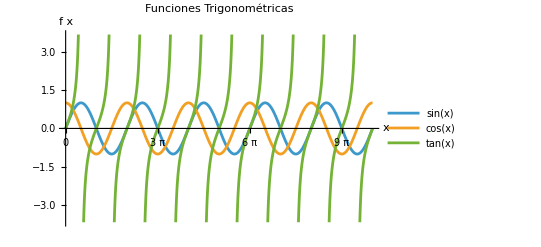

```mathematica
Plot[circulares,{x,0,10 Pi},Ticks->{Table[{n Pi,n Pi},{n,0,10}],Automatic}, PlotLabel->"Funciones Trigonométricas",PlotLegends->"Expressions",AxesLabel->{HoldForm[x],HoldForm[f (x)]},LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

```mathematica
circulares2= {Csc[x], Sec[x], Cot[x]}
```

{Csc[x],Sec[x],Cot[x]}

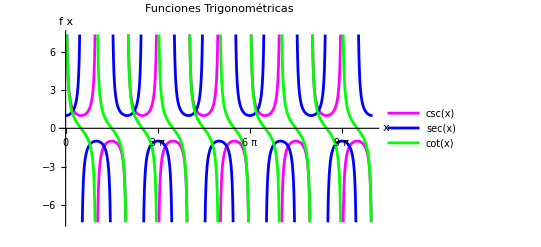

```mathematica
Plot[circulares2,{x,0,10 Pi},Ticks->{Table[{n Pi,n Pi},{n,0,10}],Automatic},PlotStyle->{Magenta, Blue, Green},PlotLabel->"Funciones Trigonométricas",PlotLegends->"Expressions",AxesLabel->{HoldForm[x],HoldForm[f (x)]},LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

Funciones trigonométricas inversas

# Rango para mejor visibilidad [-2π a 2π]

```mathematica
inversas = {ArcSin[x], ArcCos[x], ArcTan[x]}
```

{ArcSin[x],ArcCos[x],ArcTan[x]}

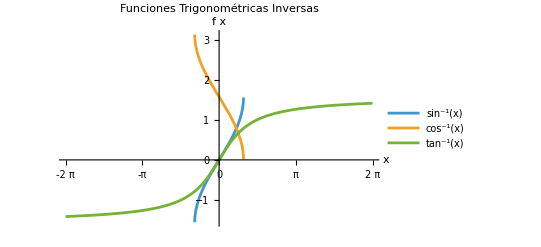

```mathematica
Plot[inversas, {x, -2π, 2π},Ticks->{Table[{n Pi,n Pi},{n,-2,2}],Automatic}, PlotLabel->"Funciones Trigonométricas Inversas", PlotLegends->"Expressions", AxesLabel->{HoldForm[x],HoldForm[f(x)]}, LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

```mathematica
inversas2 = { ArcSec[x], ArcCsc[x], ArcCot[x]}
```

{ArcSec[x],ArcCsc[x],ArcCot[x]}

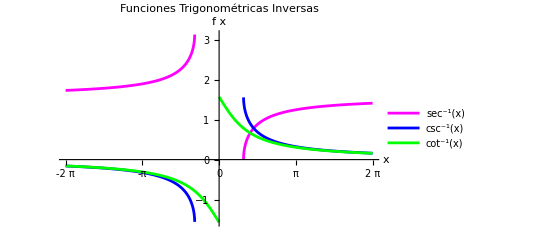

```mathematica
Plot[inversas2, {x, -2π, 2π},Ticks->{Table[{n Pi,n Pi},{n,-2,2}],Automatic}, PlotStyle->{Magenta, Blue, Green}, PlotLabel->"Funciones Trigonométricas Inversas", PlotLegends->"Expressions", AxesLabel->{HoldForm[x],HoldForm[f(x)]}, LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

Funciones trigonométricas hiperbólicas

# Rango para mejor visibilidad [-2π a 2π]

```mathematica
hiperbolicas = {Sinh[x], Cosh[x], Tanh[x]}
```

{Sinh[x],Cosh[x],Tanh[x]}

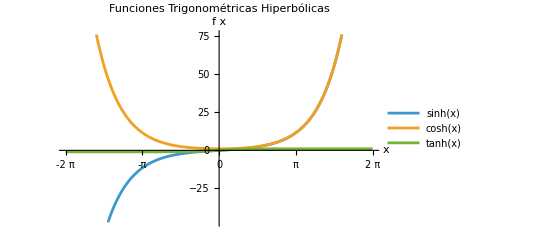

```mathematica
Plot[hiperbolicas, {x, -2π, 2π},Ticks->{Table[{n Pi,n Pi},{n,-2,2}],Automatic},PlotLabel->"Funciones Trigonométricas Hiperbólicas", PlotLegends->"Expressions", AxesLabel->{HoldForm[x],HoldForm[f(x)]}, LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

```mathematica
hiperbolicas2 ={Sech[x], Csch[x], Coth[x]}
```

{Sech[x],Csch[x],Coth[x]}

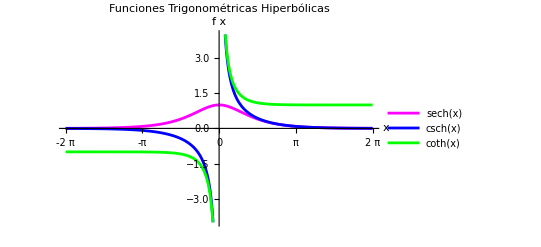

```mathematica
Plot[hiperbolicas2, {x, -2π, 2π},Ticks->{Table[{n Pi,n Pi},{n,-2,2}],Automatic}, PlotStyle->{Magenta, Blue, Green},PlotLabel->"Funciones Trigonométricas Hiperbólicas", PlotLegends->"Expressions", AxesLabel->{HoldForm[x],HoldForm[f(x)]}, LabelStyle->{FontFamily->"Roboto Serif 20pt",12,GrayLevel[0]}]
```

Graficar el log(x) de 0 a 1000.

```mathematica
Plot[Labeled[Log[x],"Log(x)",After],{x,1,1000},Filling->Bottom, FillingStyle->LightOrange, PlotStyle->Orange, AxesLabel->{HoldForm[x],HoldForm[f(x)]}]
```

-Graphics-

Graficar e^x de -10 a 10.

```mathematica
Plot[Labeled[Exp[x], "ⅇ^x", After], {x, -10, 10}, Filling->Bottom, FillingStyle->LightBlue, PlotStyle->Blue, AxesLabel->{HoldForm[x],HoldForm[f(x)]}]
```

-Graphics-

Graficar e^-x de -10 a 10.

```mathematica
Plot[Labeled[Exp[-x], "ⅇ^-x", Before], {x, -10, 10}, Filling->Bottom, FillingStyle->LightGreen, PlotStyle->Green, AxesLabel->{HoldForm[x],HoldForm[f(x)]}]
```

-Graphics-

Hacer una expansión de potencias de todas las funciones trigonométricas alrededor de cero con 10 términos cada una.

# Series de Maclaurin para el desarrollo alrededor de x=0

Funciones trigonométricas circulares estándar

```mathematica
Normal[Series[Sin[x], {x, 0, 10}]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
Normal[Series[Cos[x], {x, 0, 10}]]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800

```mathematica
Normal[Series[Tan[x], {x, 0, 10}]]
```

x+x^3/3+(2 x^5)/15+(17 x^7)/315+(62 x^9)/2835

```mathematica
Normal[Series[Sec[x], {x, 0, 10}]]
```

1+x^2/2+(5 x^4)/24+(61 x^6)/720+(277 x^8)/8064+(50521 x^10)/3628800

```mathematica
Normal[Series[Csc[x], {x, 0, 10}]]
```

1/x+x/6+(7 x^3)/360+(31 x^5)/15120+(127 x^7)/604800+(73 x^9)/3421440

```mathematica
Normal[Series[Cot[x], {x, 0, 10}]]
```

1/x-x/3-x^3/45-(2 x^5)/945-x^7/4725-(2 x^9)/93555

Funciones trigonométricas inversas

```mathematica
Normal[Series[ArcSin[x], {x, 0, 10}]]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152

```mathematica
Normal[Series[ArcCos[x], {x, 0, 10}]]
```

π/2-x-x^3/6-(3 x^5)/40-(5 x^7)/112-(35 x^9)/1152

```mathematica
Normal[Series[ArcTan[x], {x, 0, 10}]]
```

x-x^3/3+x^5/5-x^7/7+x^9/9

```mathematica
Normal[Series[ArcSec[x], {x, 0, 10}]]
```

-1/4 √(-1/x^2) x^3-3/32 √(-1/x^2) x^5-5/96 √(-1/x^2) x^7-(35 √(-1/x^2) x^9)/1024-(63 √(-1/x^2) x^11)/2560+1/2 (π+√(-1/x^2) x Log[-4/x^2])

```mathematica
Normal[Series[ArcCsc[x], {x, 0, 10}]]
```

1/4 √(-1/x^2) x^3+3/32 √(-1/x^2) x^5+5/96 √(-1/x^2) x^7+(35 √(-1/x^2) x^9)/1024+(63 √(-1/x^2) x^11)/2560-1/2 √(-1/x^2) x Log[-4/x^2]

```mathematica
Normal[Series[ArcCot[x], {x, 0, 10}]]
```

-x+1/2 π √(1/x^2) x+x^3/3-x^5/5+x^7/7-x^9/9

Funciones trigonométricas hiperbólicas

```mathematica
Normal[Series[Sinh[x], {x, 0, 10}]]
```

x+x^3/6+x^5/120+x^7/5040+x^9/362880

```mathematica
Normal[Series[Cosh[x], {x, 0, 10}]]
```

1+x^2/2+x^4/24+x^6/720+x^8/40320+x^10/3628800

```mathematica
Normal[Series[Tanh[x], {x, 0, 10}]]
```

x-x^3/3+(2 x^5)/15-(17 x^7)/315+(62 x^9)/2835

```mathematica
Normal[Series[Sech[x], {x, 0, 10}]]
```

1-x^2/2+(5 x^4)/24-(61 x^6)/720+(277 x^8)/8064-(50521 x^10)/3628800

```mathematica
Normal[Series[Csch[x], {x, 0, 10}]]
```

1/x-x/6+(7 x^3)/360-(31 x^5)/15120+(127 x^7)/604800-(73 x^9)/3421440

```mathematica
Normal[Series[Coth[x], {x, 0, 10}]]
```

1/x+x/3-x^3/45+(2 x^5)/945-x^7/4725+(2 x^9)/93555

Repetir el ejercicio anterior alrededor de x_0 = a.

# Series de Taylor para el desarrollo alrededor de un punto arbitrario x=a

Funciones trigonométricas circulares estándar

```mathematica
Normal[Series[Sin[x], {x, a, 10}]]
```

(-a+x) Cos[a]-1/6 (-a+x)^3 Cos[a]+1/120 (-a+x)^5 Cos[a]-((-a+x)^7 Cos[a])/5040+((-a+x)^9 Cos[a])/362880+Sin[a]-1/2 (-a+x)^2 Sin[a]+1/24 (-a+x)^4 Sin[a]-1/720 (-a+x)^6 Sin[a]+((-a+x)^8 Sin[a])/40320-((-a+x)^10 Sin[a])/3628800

```mathematica
Normal[Series[Cos[x], {x, a, 10}]]
```

Cos[a]-1/2 (-a+x)^2 Cos[a]+1/24 (-a+x)^4 Cos[a]-1/720 (-a+x)^6 Cos[a]+((-a+x)^8 Cos[a])/40320-((-a+x)^10 Cos[a])/3628800-(-a+x) Sin[a]+1/6 (-a+x)^3 Sin[a]-1/120 (-a+x)^5 Sin[a]+((-a+x)^7 Sin[a])/5040-((-a+x)^9 Sin[a])/362880

```mathematica
Normal[Series[Tan[x], {x, a, 10}]]
```

(-a+x) Sec[a]^2+Tan[a]+(-a+x)^2 Sec[a]^2 Tan[a]+(-a+x)^3 (1/3+Tan[a]^2/2+Tan[a] ((5 Tan[a])/6+Tan[a]^3))+(-a+x)^4 ((17 Tan[a])/24+Tan[a]^3-1/2 Tan[a] (1/2+Tan[a]^2)+Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4))+(-a+x)^5 (13/60+(29 Tan[a]^2)/24+Tan[a]^4+1/6 (-1/2-Tan[a]^2)-1/2 Tan[a] ((5 Tan[a])/6+Tan[a]^3)+Tan[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5))+(-a+x)^6 ((371 Tan[a])/720+(3 Tan[a]^3)/2+Tan[a]^5+1/24 Tan[a] (1/2+Tan[a]^2)+1/6 (-(5 Tan[a])/6-Tan[a]^3)-1/2 Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+Tan[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6))+(-a+x)^7 (71/840+(661 Tan[a]^2)/720+(11 Tan[a]^4)/6+Tan[a]^6+1/120 (1/2+Tan[a]^2)+1/24 Tan[a] ((5 Tan[a])/6+Tan[a]^3)+1/6 (-5/24-(7 Tan[a]^2)/6-Tan[a]^4)-1/2 Tan[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+Tan[a] ((277 Tan[a])/1008+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7))+(-a+x)^8 ((3691 Tan[a])/13440+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7-1/720 Tan[a] (1/2+Tan[a]^2)+1/120 ((5 Tan[a])/6+Tan[a]^3)+1/24 Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+1/6 (-(61 Tan[a])/120-(3 Tan[a]^3)/2-Tan[a]^5)-1/2 Tan[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6)+Tan[a] (277/8064+(3071 Tan[a]^2)/5040+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8))+(-a+x)^9 (6233/181440+(24569 Tan[a]^2)/40320+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8+(-1/2-Tan[a]^2)/5040-1/720 Tan[a] ((5 Tan[a])/6+Tan[a]^3)+1/120 (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+1/24 Tan[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+1/6 (-61/720-(331 Tan[a]^2)/360-(11 Tan[a]^4)/6-Tan[a]^6)-1/2 Tan[a] ((277 Tan[a])/1008+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7)+Tan[a] ((50521 Tan[a])/362880+(3403 Tan[a]^3)/3024+(203 Tan[a]^5)/72+(17 Tan[a]^7)/6+Tan[a]^9))+(-a+x)^10 ((505219 Tan[a])/3628800+(3403 Tan[a]^3)/3024+(203 Tan[a]^5)/72+(17 Tan[a]^7)/6+Tan[a]^9+(Tan[a] (1/2+Tan[a]^2))/40320+(-(5 Tan[a])/6-Tan[a]^3)/5040-1/720 Tan[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+1/120 ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+1/24 Tan[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6)+1/6 (-(277 Tan[a])/1008-(173 Tan[a]^3)/120-(13 Tan[a]^5)/6-Tan[a]^7)-1/2 Tan[a] (277/8064+(3071 Tan[a]^2)/5040+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8)+Tan[a] (50521/3628800+(94723 Tan[a]^2)/259200+(28121 Tan[a]^4)/15120+(147 Tan[a]^6)/40+(19 Tan[a]^8)/6+Tan[a]^10))

```mathematica
Normal[Series[Sec[x], {x, a, 10}]]
```

Sec[a]+(-a+x) Sec[a] Tan[a]+(-a+x)^2 Sec[a] (1/2+Tan[a]^2)+(-a+x)^3 Sec[a] ((5 Tan[a])/6+Tan[a]^3)+(-a+x)^4 Sec[a] (5/24+(7 Tan[a]^2)/6+Tan[a]^4)+(-a+x)^5 Sec[a] ((61 Tan[a])/120+(3 Tan[a]^3)/2+Tan[a]^5)+(-a+x)^6 Sec[a] (61/720+(331 Tan[a]^2)/360+(11 Tan[a]^4)/6+Tan[a]^6)+(-a+x)^7 Sec[a] ((277 Tan[a])/1008+(173 Tan[a]^3)/120+(13 Tan[a]^5)/6+Tan[a]^7)+(-a+x)^8 Sec[a] (277/8064+(3071 Tan[a]^2)/5040+(83 Tan[a]^4)/40+(5 Tan[a]^6)/2+Tan[a]^8)+(-a+x)^9 Sec[a] ((50521 Tan[a])/362880+(3403 Tan[a]^3)/3024+(203 Tan[a]^5)/72+(17 Tan[a]^7)/6+Tan[a]^9)+(-a+x)^10 Sec[a] (50521/3628800+(94723 Tan[a]^2)/259200+(28121 Tan[a]^4)/15120+(147 Tan[a]^6)/40+(19 Tan[a]^8)/6+Tan[a]^10)

```mathematica
Normal[Series[Csc[x], {x, a, 10}]]
```

Csc[a]-(-a+x) Cot[a] Csc[a]+(-a+x)^2 (1/2+Cot[a]^2) Csc[a]+(-a+x)^3 (-(5 Cot[a])/6-Cot[a]^3) Csc[a]+(-a+x)^4 (5/24+(7 Cot[a]^2)/6+Cot[a]^4) Csc[a]+(-a+x)^5 (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5) Csc[a]+(-a+x)^6 (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6) Csc[a]+(-a+x)^7 (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7) Csc[a]+(-a+x)^8 (277/8064+(3071 Cot[a]^2)/5040+(83 Cot[a]^4)/40+(5 Cot[a]^6)/2+Cot[a]^8) Csc[a]+(-a+x)^9 (-(50521 Cot[a])/362880-(3403 Cot[a]^3)/3024-(203 Cot[a]^5)/72-(17 Cot[a]^7)/6-Cot[a]^9) Csc[a]+(-a+x)^10 (50521/3628800+(94723 Cot[a]^2)/259200+(28121 Cot[a]^4)/15120+(147 Cot[a]^6)/40+(19 Cot[a]^8)/6+Cot[a]^10) Csc[a]

```mathematica
Normal[Series[Cot[x], {x, a, 10}]]
```

Cot[a]+(-a+x)^3 (-1/3-Cot[a]^2/2+Cot[a] (-(5 Cot[a])/6-Cot[a]^3))+(-a+x)^4 ((17 Cot[a])/24+Cot[a]^3-1/2 Cot[a] (1/2+Cot[a]^2)+Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4))+(-a+x)^5 (-13/60-(29 Cot[a]^2)/24-Cot[a]^4+1/6 (1/2+Cot[a]^2)-1/2 Cot[a] (-(5 Cot[a])/6-Cot[a]^3)+Cot[a] (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5))+(-a+x)^6 ((371 Cot[a])/720+(3 Cot[a]^3)/2+Cot[a]^5+1/24 Cot[a] (1/2+Cot[a]^2)+1/6 (-(5 Cot[a])/6-Cot[a]^3)-1/2 Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4)+Cot[a] (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6))+(-a+x)^7 (-71/840-(661 Cot[a]^2)/720-(11 Cot[a]^4)/6-Cot[a]^6+1/120 (-1/2-Cot[a]^2)+1/24 Cot[a] (-(5 Cot[a])/6-Cot[a]^3)+1/6 (5/24+(7 Cot[a]^2)/6+Cot[a]^4)-1/2 Cot[a] (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5)+Cot[a] (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7))+(-a+x)^8 ((3691 Cot[a])/13440+(173 Cot[a]^3)/120+(13 Cot[a]^5)/6+Cot[a]^7-1/720 Cot[a] (1/2+Cot[a]^2)+1/120 ((5 Cot[a])/6+Cot[a]^3)+1/24 Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4)+1/6 (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5)-1/2 Cot[a] (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6)+Cot[a] (277/8064+(3071 Cot[a]^2)/5040+(83 Cot[a]^4)/40+(5 Cot[a]^6)/2+Cot[a]^8))+(-a+x)^9 (-6233/181440-(24569 Cot[a]^2)/40320-(83 Cot[a]^4)/40-(5 Cot[a]^6)/2-Cot[a]^8+(1/2+Cot[a]^2)/5040-1/720 Cot[a] (-(5 Cot[a])/6-Cot[a]^3)+1/120 (-5/24-(7 Cot[a]^2)/6-Cot[a]^4)+1/24 Cot[a] (-(61 Cot[a])/120-(3 Cot[a]^3)/2-Cot[a]^5)+1/6 (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6)-1/2 Cot[a] (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7)+Cot[a] (-(50521 Cot[a])/362880-(3403 Cot[a]^3)/3024-(203 Cot[a]^5)/72-(17 Cot[a]^7)/6-Cot[a]^9))+(-a+x)^10 ((505219 Cot[a])/3628800+(3403 Cot[a]^3)/3024+(203 Cot[a]^5)/72+(17 Cot[a]^7)/6+Cot[a]^9+(Cot[a] (1/2+Cot[a]^2))/40320+(-(5 Cot[a])/6-Cot[a]^3)/5040-1/720 Cot[a] (5/24+(7 Cot[a]^2)/6+Cot[a]^4)+1/120 ((61 Cot[a])/120+(3 Cot[a]^3)/2+Cot[a]^5)+1/24 Cot[a] (61/720+(331 Cot[a]^2)/360+(11 Cot[a]^4)/6+Cot[a]^6)+1/6 (-(277 Cot[a])/1008-(173 Cot[a]^3)/120-(13 Cot[a]^5)/6-Cot[a]^7)-1/2 Cot[a] (277/8064+(3071 Cot[a]^2)/5040+(83 Cot[a]^4)/40+(5 Cot[a]^6)/2+Cot[a]^8)+Cot[a] (50521/3628800+(94723 Cot[a]^2)/259200+(28121 Cot[a]^4)/15120+(147 Cot[a]^6)/40+(19 Cot[a]^8)/6+Cot[a]^10))-(-a+x) Csc[a]^2+(-a+x)^2 Cot[a] Csc[a]^2

Funciones trigonométricas inversas

```mathematica
Normal[Series[ArcSin[x], {x, a, 10}]]
```

(-a+x)/(√(1-a^2))+(a (-a+x)^2)/(2 (1-a^2)^(3/2))+((1+2 a^2) (-a+x)^3)/(6 (1-a^2)^(5/2))+(a (3+2 a^2) (-a+x)^4)/(8 (1-a^2)^(7/2))+((3+24 a^2+8 a^4) (-a+x)^5)/(40 (1-a^2)^(9/2))+(a (15+40 a^2+8 a^4) (-a+x)^6)/(48 (1-a^2)^(11/2))+((5+90 a^2+120 a^4+16 a^6) (-a+x)^7)/(112 (1-a^2)^(13/2))+(a (35+210 a^2+168 a^4+16 a^6) (-a+x)^8)/(128 (1-a^2)^(15/2))+((35+1120 a^2+3360 a^4+1792 a^6+128 a^8) (-a+x)^9)/(1152 (1-a^2)^(17/2))-(a (315+3360 a^2+6048 a^4+2304 a^6+128 a^8) (-a+x)^10)/(1280 √(1-a^2) (-1+a^2)^9)+ArcSin[a]

```mathematica
Normal[Series[ArcCos[x], {x, a, 10}]]
```

-(-a+x)/(√(1-a^2))-(a (-a+x)^2)/(2 (1-a^2)^(3/2))-((1+2 a^2) (-a+x)^3)/(6 (1-a^2)^(5/2))-(a (3+2 a^2) (-a+x)^4)/(8 (1-a^2)^(7/2))-((3+24 a^2+8 a^4) (-a+x)^5)/(40 (1-a^2)^(9/2))-(a (15+40 a^2+8 a^4) (-a+x)^6)/(48 (1-a^2)^(11/2))-((5+90 a^2+120 a^4+16 a^6) (-a+x)^7)/(112 (1-a^2)^(13/2))-(a (35+210 a^2+168 a^4+16 a^6) (-a+x)^8)/(128 (1-a^2)^(15/2))-((35+1120 a^2+3360 a^4+1792 a^6+128 a^8) (-a+x)^9)/(1152 (1-a^2)^(17/2))+(a (315+3360 a^2+6048 a^4+2304 a^6+128 a^8) (-a+x)^10)/(1280 √(1-a^2) (-1+a^2)^9)+ArcCos[a]

```mathematica
Normal[Series[ArcTan[x], {x, a, 10}]]
```

(-a+x)/(1+a^2)-(a (-a+x)^2)/((1+a^2)^2)+(((4 a^2)/((1+a^2)^2)-1/(1+a^2)) (-a+x)^3)/(3 (1+a^2))+((-(8 a^3)/((1+a^2)^3)+(4 a)/((1+a^2)^2)) (-a+x)^4)/(4 (1+a^2))+(((16 a^4)/((1+a^2)^4)-(12 a^2)/((1+a^2)^3)+1/((1+a^2)^2)) (-a+x)^5)/(5 (1+a^2))+((-(32 a^5)/((1+a^2)^5)+(32 a^3)/((1+a^2)^4)-(6 a)/((1+a^2)^3)) (-a+x)^6)/(6 (1+a^2))+(((64 a^6)/((1+a^2)^6)-(80 a^4)/((1+a^2)^5)+(24 a^2)/((1+a^2)^4)-1/((1+a^2)^3)) (-a+x)^7)/(7 (1+a^2))+((-(128 a^7)/((1+a^2)^7)+(192 a^5)/((1+a^2)^6)-(80 a^3)/((1+a^2)^5)+(8 a)/((1+a^2)^4)) (-a+x)^8)/(8 (1+a^2))+(((256 a^8)/((1+a^2)^8)-(448 a^6)/((1+a^2)^7)+(240 a^4)/((1+a^2)^6)-(40 a^2)/((1+a^2)^5)+1/((1+a^2)^4)) (-a+x)^9)/(9 (1+a^2))+((-(512 a^9)/((1+a^2)^9)+(1024 a^7)/((1+a^2)^8)-(672 a^5)/((1+a^2)^7)+(160 a^3)/((1+a^2)^6)-(10 a)/((1+a^2)^5)) (-a+x)^10)/(10 (1+a^2))+ArcTan[a]

```mathematica
Normal[Series[ArcSec[x], {x, a, 10}]]
```

(-a+x)/(√(1-1/a^2) a^2)+((1-2 a^2) (-a+x)^2)/(2 a^3 (-1+a^2) √((-1+a^2)/a^2))+1/6 (3/((1-1/a^2)^(5/2) a^8)+7/((1-1/a^2)^(3/2) a^6)+6/(√(1-1/a^2) a^4)) (-a+x)^3+1/24 (-15/((1-1/a^2)^(7/2) a^11)-45/((1-1/a^2)^(5/2) a^9)-48/((1-1/a^2)^(3/2) a^7)-24/(√(1-1/a^2) a^5)) (-a+x)^4+1/120 (105/((1-1/a^2)^(9/2) a^14)+390/((1-1/a^2)^(7/2) a^12)+549/((1-1/a^2)^(5/2) a^10)+360/((1-1/a^2)^(3/2) a^8)+120/(√(1-1/a^2) a^6)) (-a+x)^5+1/720 (-945/((1-1/a^2)^(11/2) a^17)-4200/((1-1/a^2)^(9/2) a^15)-7425/((1-1/a^2)^(7/2) a^13)-6570/((1-1/a^2)^(5/2) a^11)-3000/((1-1/a^2)^(3/2) a^9)-720/(√(1-1/a^2) a^7)) (-a+x)^6+((10395/((1-1/a^2)^(13/2) a^20)+53865/((1-1/a^2)^(11/2) a^18)+114975/((1-1/a^2)^(9/2) a^16)+129375/((1-1/a^2)^(7/2) a^14)+81270/((1-1/a^2)^(5/2) a^12)+27720/((1-1/a^2)^(3/2) a^10)+5040/(√(1-1/a^2) a^8)) (-a+x)^7)/5040+((-135135/((1-1/a^2)^(15/2) a^23)-800415/((1-1/a^2)^(13/2) a^21)-2004345/((1-1/a^2)^(11/2) a^19)-2745225/((1-1/a^2)^(9/2) a^17)-2217600/((1-1/a^2)^(7/2) a^15)-1058400/((1-1/a^2)^(5/2) a^13)-282240/((1-1/a^2)^(3/2) a^11)-40320/(√(1-1/a^2) a^9)) (-a+x)^8)/40320+((2027025/((1-1/a^2)^(17/2) a^26)+13513500/((1-1/a^2)^(15/2) a^24)+38856510/((1-1/a^2)^(13/2) a^22)+62789580/((1-1/a^2)^(11/2) a^20)+62192025/((1-1/a^2)^(9/2) a^18)+38556000/((1-1/a^2)^(7/2) a^16)+14605920/((1-1/a^2)^(5/2) a^14)+3144960/((1-1/a^2)^(3/2) a^12)+362880/(√(1-1/a^2) a^10)) (-a+x)^9)/362880-((-128+1216 a^2-5168 a^4+12920 a^6-20995 a^8+23126 a^10-16032 a^12+14016 a^14+1920 a^16+1280 a^18) (-a+x)^10)/(1280 a^11 (-1+a^2)^9 √((-1+a^2)/a^2))+ArcSec[a]

```mathematica
Normal[Series[ArcCsc[x], {x, a, 10}]]
```

-(-a+x)/(√(1-1/a^2) a^2)+((-1+2 a^2) (-a+x)^2)/(2 a^3 (-1+a^2) √((-1+a^2)/a^2))+1/6 (-3/((1-1/a^2)^(5/2) a^8)-7/((1-1/a^2)^(3/2) a^6)-6/(√(1-1/a^2) a^4)) (-a+x)^3+1/24 (15/((1-1/a^2)^(7/2) a^11)+45/((1-1/a^2)^(5/2) a^9)+48/((1-1/a^2)^(3/2) a^7)+24/(√(1-1/a^2) a^5)) (-a+x)^4+1/120 (-105/((1-1/a^2)^(9/2) a^14)-390/((1-1/a^2)^(7/2) a^12)-549/((1-1/a^2)^(5/2) a^10)-360/((1-1/a^2)^(3/2) a^8)-120/(√(1-1/a^2) a^6)) (-a+x)^5+1/720 (945/((1-1/a^2)^(11/2) a^17)+4200/((1-1/a^2)^(9/2) a^15)+7425/((1-1/a^2)^(7/2) a^13)+6570/((1-1/a^2)^(5/2) a^11)+3000/((1-1/a^2)^(3/2) a^9)+720/(√(1-1/a^2) a^7)) (-a+x)^6+((-10395/((1-1/a^2)^(13/2) a^20)-53865/((1-1/a^2)^(11/2) a^18)-114975/((1-1/a^2)^(9/2) a^16)-129375/((1-1/a^2)^(7/2) a^14)-81270/((1-1/a^2)^(5/2) a^12)-27720/((1-1/a^2)^(3/2) a^10)-5040/(√(1-1/a^2) a^8)) (-a+x)^7)/5040+((135135/((1-1/a^2)^(15/2) a^23)+800415/((1-1/a^2)^(13/2) a^21)+2004345/((1-1/a^2)^(11/2) a^19)+2745225/((1-1/a^2)^(9/2) a^17)+2217600/((1-1/a^2)^(7/2) a^15)+1058400/((1-1/a^2)^(5/2) a^13)+282240/((1-1/a^2)^(3/2) a^11)+40320/(√(1-1/a^2) a^9)) (-a+x)^8)/40320+((-2027025/((1-1/a^2)^(17/2) a^26)-13513500/((1-1/a^2)^(15/2) a^24)-38856510/((1-1/a^2)^(13/2) a^22)-62789580/((1-1/a^2)^(11/2) a^20)-62192025/((1-1/a^2)^(9/2) a^18)-38556000/((1-1/a^2)^(7/2) a^16)-14605920/((1-1/a^2)^(5/2) a^14)-3144960/((1-1/a^2)^(3/2) a^12)-362880/(√(1-1/a^2) a^10)) (-a+x)^9)/362880+((-128+1216 a^2-5168 a^4+12920 a^6-20995 a^8+23126 a^10-16032 a^12+14016 a^14+1920 a^16+1280 a^18) (-a+x)^10)/(1280 a^11 (-1+a^2)^9 √((-1+a^2)/a^2))+ArcCsc[a]

```mathematica
Normal[Series[ArcCot[x], {x, a, 10}]]
```

(-a+x)/(-1-a^2)+(a (-a+x)^2)/((1+a^2)^2)+1/3 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)-(4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4))/((1+1/a^2) a^2)) (-a+x)^3+1/4 (-6/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5)+(2 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)))/((1+1/a^2) a^3)-(8/((1+1/a^2)^3 a^9)-12/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5))/((1+1/a^2) a^2)) (-a+x)^4+1/5 (8/((1+1/a^2)^2 a^8)-5/((1+1/a^2) a^6)-(3 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)))/((1+1/a^2) a^4)+(2 (8/((1+1/a^2)^3 a^9)-12/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5)))/((1+1/a^2) a^3)-(16/((1+1/a^2)^4 a^12)-36/((1+1/a^2)^3 a^10)+25/((1+1/a^2)^2 a^8)-5/((1+1/a^2) a^6))/((1+1/a^2) a^2)) (-a+x)^5+1/6 (-10/((1+1/a^2)^2 a^9)+6/((1+1/a^2) a^7)+(4 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)))/((1+1/a^2) a^5)-(3 (8/((1+1/a^2)^3 a^9)-12/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5)))/((1+1/a^2) a^4)+(2 (16/((1+1/a^2)^4 a^12)-36/((1+1/a^2)^3 a^10)+25/((1+1/a^2)^2 a^8)-5/((1+1/a^2) a^6)))/((1+1/a^2) a^3)-(32/((1+1/a^2)^5 a^15)-96/((1+1/a^2)^4 a^13)+102/((1+1/a^2)^3 a^11)-44/((1+1/a^2)^2 a^9)+6/((1+1/a^2) a^7))/((1+1/a^2) a^2)) (-a+x)^6+1/7 (12/((1+1/a^2)^2 a^10)-7/((1+1/a^2) a^8)-(5 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)))/((1+1/a^2) a^6)+(4 (8/((1+1/a^2)^3 a^9)-12/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5)))/((1+1/a^2) a^5)-(3 (16/((1+1/a^2)^4 a^12)-36/((1+1/a^2)^3 a^10)+25/((1+1/a^2)^2 a^8)-5/((1+1/a^2) a^6)))/((1+1/a^2) a^4)+(2 (32/((1+1/a^2)^5 a^15)-96/((1+1/a^2)^4 a^13)+102/((1+1/a^2)^3 a^11)-44/((1+1/a^2)^2 a^9)+6/((1+1/a^2) a^7)))/((1+1/a^2) a^3)-(64/((1+1/a^2)^6 a^18)-240/((1+1/a^2)^5 a^16)+344/((1+1/a^2)^4 a^14)-231/((1+1/a^2)^3 a^12)+70/((1+1/a^2)^2 a^10)-7/((1+1/a^2) a^8))/((1+1/a^2) a^2)) (-a+x)^7+1/8 (-14/((1+1/a^2)^2 a^11)+8/((1+1/a^2) a^9)+(6 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)))/((1+1/a^2) a^7)-(5 (8/((1+1/a^2)^3 a^9)-12/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5)))/((1+1/a^2) a^6)+(4 (16/((1+1/a^2)^4 a^12)-36/((1+1/a^2)^3 a^10)+25/((1+1/a^2)^2 a^8)-5/((1+1/a^2) a^6)))/((1+1/a^2) a^5)-(3 (32/((1+1/a^2)^5 a^15)-96/((1+1/a^2)^4 a^13)+102/((1+1/a^2)^3 a^11)-44/((1+1/a^2)^2 a^9)+6/((1+1/a^2) a^7)))/((1+1/a^2) a^4)+(2 (64/((1+1/a^2)^6 a^18)-240/((1+1/a^2)^5 a^16)+344/((1+1/a^2)^4 a^14)-231/((1+1/a^2)^3 a^12)+70/((1+1/a^2)^2 a^10)-7/((1+1/a^2) a^8)))/((1+1/a^2) a^3)-(128/((1+1/a^2)^7 a^21)-576/((1+1/a^2)^6 a^19)+1040/((1+1/a^2)^5 a^17)-952/((1+1/a^2)^4 a^15)+456/((1+1/a^2)^3 a^13)-104/((1+1/a^2)^2 a^11)+8/((1+1/a^2) a^9))/((1+1/a^2) a^2)) (-a+x)^8+1/9 (16/((1+1/a^2)^2 a^12)-9/((1+1/a^2) a^10)-(7 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)))/((1+1/a^2) a^8)+(6 (8/((1+1/a^2)^3 a^9)-12/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5)))/((1+1/a^2) a^7)-(5 (16/((1+1/a^2)^4 a^12)-36/((1+1/a^2)^3 a^10)+25/((1+1/a^2)^2 a^8)-5/((1+1/a^2) a^6)))/((1+1/a^2) a^6)+(4 (32/((1+1/a^2)^5 a^15)-96/((1+1/a^2)^4 a^13)+102/((1+1/a^2)^3 a^11)-44/((1+1/a^2)^2 a^9)+6/((1+1/a^2) a^7)))/((1+1/a^2) a^5)-(3 (64/((1+1/a^2)^6 a^18)-240/((1+1/a^2)^5 a^16)+344/((1+1/a^2)^4 a^14)-231/((1+1/a^2)^3 a^12)+70/((1+1/a^2)^2 a^10)-7/((1+1/a^2) a^8)))/((1+1/a^2) a^4)+(2 (128/((1+1/a^2)^7 a^21)-576/((1+1/a^2)^6 a^19)+1040/((1+1/a^2)^5 a^17)-952/((1+1/a^2)^4 a^15)+456/((1+1/a^2)^3 a^13)-104/((1+1/a^2)^2 a^11)+8/((1+1/a^2) a^9)))/((1+1/a^2) a^3)-(256/((1+1/a^2)^8 a^24)-1344/((1+1/a^2)^7 a^22)+2928/((1+1/a^2)^6 a^20)-3400/((1+1/a^2)^5 a^18)+2241/((1+1/a^2)^4 a^16)-819/((1+1/a^2)^3 a^14)+147/((1+1/a^2)^2 a^12)-9/((1+1/a^2) a^10))/((1+1/a^2) a^2)) (-a+x)^9+1/10 (-18/((1+1/a^2)^2 a^13)+10/((1+1/a^2) a^11)+(8 (4/((1+1/a^2)^2 a^6)-3/((1+1/a^2) a^4)))/((1+1/a^2) a^9)-(7 (8/((1+1/a^2)^3 a^9)-12/((1+1/a^2)^2 a^7)+4/((1+1/a^2) a^5)))/((1+1/a^2) a^8)+(6 (16/((1+1/a^2)^4 a^12)-36/((1+1/a^2)^3 a^10)+25/((1+1/a^2)^2 a^8)-5/((1+1/a^2) a^6)))/((1+1/a^2) a^7)-(5 (32/((1+1/a^2)^5 a^15)-96/((1+1/a^2)^4 a^13)+102/((1+1/a^2)^3 a^11)-44/((1+1/a^2)^2 a^9)+6/((1+1/a^2) a^7)))/((1+1/a^2) a^6)+(4 (64/((1+1/a^2)^6 a^18)-240/((1+1/a^2)^5 a^16)+344/((1+1/a^2)^4 a^14)-231/((1+1/a^2)^3 a^12)+70/((1+1/a^2)^2 a^10)-7/((1+1/a^2) a^8)))/((1+1/a^2) a^5)-(3 (128/((1+1/a^2)^7 a^21)-576/((1+1/a^2)^6 a^19)+1040/((1+1/a^2)^5 a^17)-952/((1+1/a^2)^4 a^15)+456/((1+1/a^2)^3 a^13)-104/((1+1/a^2)^2 a^11)+8/((1+1/a^2) a^9)))/((1+1/a^2) a^4)+(2 (256/((1+1/a^2)^8 a^24)-1344/((1+1/a^2)^7 a^22)+2928/((1+1/a^2)^6 a^20)-3400/((1+1/a^2)^5 a^18)+2241/((1+1/a^2)^4 a^16)-819/((1+1/a^2)^3 a^14)+147/((1+1/a^2)^2 a^12)-9/((1+1/a^2) a^10)))/((1+1/a^2) a^3)-(512/((1+1/a^2)^9 a^27)-3072/((1+1/a^2)^8 a^25)+7840/((1+1/a^2)^7 a^23)-11040/((1+1/a^2)^6 a^21)+9290/((1+1/a^2)^5 a^19)-4712/((1+1/a^2)^4 a^17)+1372/((1+1/a^2)^3 a^15)-200/((1+1/a^2)^2 a^13)+10/((1+1/a^2) a^11))/((1+1/a^2) a^2)) (-a+x)^10+ArcTan[1/a]

Funciones trigonométricas hiperbólicas

```mathematica
Normal[Series[Sinh[x], {x, a, 10}]]
```

(-a+x) Cosh[a]+1/6 (-a+x)^3 Cosh[a]+1/120 (-a+x)^5 Cosh[a]+((-a+x)^7 Cosh[a])/5040+((-a+x)^9 Cosh[a])/362880+Sinh[a]+1/2 (-a+x)^2 Sinh[a]+1/24 (-a+x)^4 Sinh[a]+1/720 (-a+x)^6 Sinh[a]+((-a+x)^8 Sinh[a])/40320+((-a+x)^10 Sinh[a])/3628800

```mathematica
Normal[Series[Cosh[x], {x, a, 10}]]
```

Cosh[a]+1/2 (-a+x)^2 Cosh[a]+1/24 (-a+x)^4 Cosh[a]+1/720 (-a+x)^6 Cosh[a]+((-a+x)^8 Cosh[a])/40320+((-a+x)^10 Cosh[a])/3628800+(-a+x) Sinh[a]+1/6 (-a+x)^3 Sinh[a]+1/120 (-a+x)^5 Sinh[a]+((-a+x)^7 Sinh[a])/5040+((-a+x)^9 Sinh[a])/362880

```mathematica
Normal[Series[Tanh[x], {x, a, 10}]]
```

(-a+x) Sech[a]^2+Tanh[a]-(-a+x)^2 Sech[a]^2 Tanh[a]+(-a+x)^3 (-1/3+Tanh[a]^2/2+Tanh[a] ((5 Tanh[a])/6-Tanh[a]^3))+(-a+x)^4 ((17 Tanh[a])/24-Tanh[a]^3+1/2 Tanh[a] (-1/2+Tanh[a]^2)+Tanh[a] (5/24-(7 Tanh[a]^2)/6+Tanh[a]^4))+(-a+x)^5 (13/60-(29 Tanh[a]^2)/24+Tanh[a]^4+1/6 (-1/2+Tanh[a]^2)+1/2 Tanh[a] ((5 Tanh[a])/6-Tanh[a]^3)+Tanh[a] (-(61 Tanh[a])/120+(3 Tanh[a]^3)/2-Tanh[a]^5))+(-a+x)^6 (-(371 Tanh[a])/720+(3 Tanh[a]^3)/2-Tanh[a]^5+1/24 Tanh[a] (-1/2+Tanh[a]^2)+1/6 ((5 Tanh[a])/6-Tanh[a]^3)+1/2 Tanh[a] (5/24-(7 Tanh[a]^2)/6+Tanh[a]^4)+Tanh[a] (-61/720+(331 Tanh[a]^2)/360-(11 Tanh[a]^4)/6+Tanh[a]^6))+(-a+x)^7 (-71/840+(661 Tanh[a]^2)/720-(11 Tanh[a]^4)/6+Tanh[a]^6+1/120 (-1/2+Tanh[a]^2)+1/24 Tanh[a] ((5 Tanh[a])/6-Tanh[a]^3)+1/6 (5/24-(7 Tanh[a]^2)/6+Tanh[a]^4)+1/2 Tanh[a] (-(61 Tanh[a])/120+(3 Tanh[a]^3)/2-Tanh[a]^5)+Tanh[a] ((277 Tanh[a])/1008-(173 Tanh[a]^3)/120+(13 Tanh[a]^5)/6-Tanh[a]^7))+(-a+x)^8 ((3691 Tanh[a])/13440-(173 Tanh[a]^3)/120+(13 Tanh[a]^5)/6-Tanh[a]^7+1/720 Tanh[a] (-1/2+Tanh[a]^2)+1/120 ((5 Tanh[a])/6-Tanh[a]^3)+1/24 Tanh[a] (5/24-(7 Tanh[a]^2)/6+Tanh[a]^4)+1/6 (-(61 Tanh[a])/120+(3 Tanh[a]^3)/2-Tanh[a]^5)+1/2 Tanh[a] (-61/720+(331 Tanh[a]^2)/360-(11 Tanh[a]^4)/6+Tanh[a]^6)+Tanh[a] (277/8064-(3071 Tanh[a]^2)/5040+(83 Tanh[a]^4)/40-(5 Tanh[a]^6)/2+Tanh[a]^8))+(-a+x)^9 (6233/181440-(24569 Tanh[a]^2)/40320+(83 Tanh[a]^4)/40-(5 Tanh[a]^6)/2+Tanh[a]^8+(-1/2+Tanh[a]^2)/5040+1/720 Tanh[a] ((5 Tanh[a])/6-Tanh[a]^3)+1/120 (5/24-(7 Tanh[a]^2)/6+Tanh[a]^4)+1/24 Tanh[a] (-(61 Tanh[a])/120+(3 Tanh[a]^3)/2-Tanh[a]^5)+1/6 (-61/720+(331 Tanh[a]^2)/360-(11 Tanh[a]^4)/6+Tanh[a]^6)+1/2 Tanh[a] ((277 Tanh[a])/1008-(173 Tanh[a]^3)/120+(13 Tanh[a]^5)/6-Tanh[a]^7)+Tanh[a] (-(50521 Tanh[a])/362880+(3403 Tanh[a]^3)/3024-(203 Tanh[a]^5)/72+(17 Tanh[a]^7)/6-Tanh[a]^9))+(-a+x)^10 (-(505219 Tanh[a])/3628800+(3403 Tanh[a]^3)/3024-(203 Tanh[a]^5)/72+(17 Tanh[a]^7)/6-Tanh[a]^9+(Tanh[a] (-1/2+Tanh[a]^2))/40320+((5 Tanh[a])/6-Tanh[a]^3)/5040+1/720 Tanh[a] (5/24-(7 Tanh[a]^2)/6+Tanh[a]^4)+1/120 (-(61 Tanh[a])/120+(3 Tanh[a]^3)/2-Tanh[a]^5)+1/24 Tanh[a] (-61/720+(331 Tanh[a]^2)/360-(11 Tanh[a]^4)/6+Tanh[a]^6)+1/6 ((277 Tanh[a])/1008-(173 Tanh[a]^3)/120+(13 Tanh[a]^5)/6-Tanh[a]^7)+1/2 Tanh[a] (277/8064-(3071 Tanh[a]^2)/5040+(83 Tanh[a]^4)/40-(5 Tanh[a]^6)/2+Tanh[a]^8)+Tanh[a] (-50521/3628800+(94723 Tanh[a]^2)/259200-(28121 Tanh[a]^4)/15120+(147 Tanh[a]^6)/40-(19 Tanh[a]^8)/6+Tanh[a]^10))

```mathematica
Normal[Series[Sech[x], {x, a, 10}]]
```

Sech[a]-(-a+x) Sech[a] Tanh[a]+(-a+x)^2 Sech[a] (-1/2+Tanh[a]^2)+(-a+x)^3 Sech[a] ((5 Tanh[a])/6-Tanh[a]^3)+(-a+x)^4 Sech[a] (5/24-(7 Tanh[a]^2)/6+Tanh[a]^4)+(-a+x)^5 Sech[a] (-(61 Tanh[a])/120+(3 Tanh[a]^3)/2-Tanh[a]^5)+(-a+x)^6 Sech[a] (-61/720+(331 Tanh[a]^2)/360-(11 Tanh[a]^4)/6+Tanh[a]^6)+(-a+x)^7 Sech[a] ((277 Tanh[a])/1008-(173 Tanh[a]^3)/120+(13 Tanh[a]^5)/6-Tanh[a]^7)+(-a+x)^8 Sech[a] (277/8064-(3071 Tanh[a]^2)/5040+(83 Tanh[a]^4)/40-(5 Tanh[a]^6)/2+Tanh[a]^8)+(-a+x)^9 Sech[a] (-(50521 Tanh[a])/362880+(3403 Tanh[a]^3)/3024-(203 Tanh[a]^5)/72+(17 Tanh[a]^7)/6-Tanh[a]^9)+(-a+x)^10 Sech[a] (-50521/3628800+(94723 Tanh[a]^2)/259200-(28121 Tanh[a]^4)/15120+(147 Tanh[a]^6)/40-(19 Tanh[a]^8)/6+Tanh[a]^10)

```mathematica
Normal[Series[Csch[x], {x, a, 10}]]
```

Csch[a]-(-a+x) Coth[a] Csch[a]+(-a+x)^2 (-1/2+Coth[a]^2) Csch[a]+(-a+x)^3 ((5 Coth[a])/6-Coth[a]^3) Csch[a]+(-a+x)^4 (5/24-(7 Coth[a]^2)/6+Coth[a]^4) Csch[a]+(-a+x)^5 (-(61 Coth[a])/120+(3 Coth[a]^3)/2-Coth[a]^5) Csch[a]+(-a+x)^6 (-61/720+(331 Coth[a]^2)/360-(11 Coth[a]^4)/6+Coth[a]^6) Csch[a]+(-a+x)^7 ((277 Coth[a])/1008-(173 Coth[a]^3)/120+(13 Coth[a]^5)/6-Coth[a]^7) Csch[a]+(-a+x)^8 (277/8064-(3071 Coth[a]^2)/5040+(83 Coth[a]^4)/40-(5 Coth[a]^6)/2+Coth[a]^8) Csch[a]+(-a+x)^9 (-(50521 Coth[a])/362880+(3403 Coth[a]^3)/3024-(203 Coth[a]^5)/72+(17 Coth[a]^7)/6-Coth[a]^9) Csch[a]+(-a+x)^10 (-50521/3628800+(94723 Coth[a]^2)/259200-(28121 Coth[a]^4)/15120+(147 Coth[a]^6)/40-(19 Coth[a]^8)/6+Coth[a]^10) Csch[a]

```mathematica
Normal[Series[Coth[x], {x, a, 10}]]
```

Coth[a]+(-a+x)^3 (-1/3+Coth[a]^2/2+Coth[a] ((5 Coth[a])/6-Coth[a]^3))+(-a+x)^4 ((17 Coth[a])/24-Coth[a]^3+1/2 Coth[a] (-1/2+Coth[a]^2)+Coth[a] (5/24-(7 Coth[a]^2)/6+Coth[a]^4))+(-a+x)^5 (13/60-(29 Coth[a]^2)/24+Coth[a]^4+1/6 (-1/2+Coth[a]^2)+1/2 Coth[a] ((5 Coth[a])/6-Coth[a]^3)+Coth[a] (-(61 Coth[a])/120+(3 Coth[a]^3)/2-Coth[a]^5))+(-a+x)^6 (-(371 Coth[a])/720+(3 Coth[a]^3)/2-Coth[a]^5+1/24 Coth[a] (-1/2+Coth[a]^2)+1/6 ((5 Coth[a])/6-Coth[a]^3)+1/2 Coth[a] (5/24-(7 Coth[a]^2)/6+Coth[a]^4)+Coth[a] (-61/720+(331 Coth[a]^2)/360-(11 Coth[a]^4)/6+Coth[a]^6))+(-a+x)^7 (-71/840+(661 Coth[a]^2)/720-(11 Coth[a]^4)/6+Coth[a]^6+1/120 (-1/2+Coth[a]^2)+1/24 Coth[a] ((5 Coth[a])/6-Coth[a]^3)+1/6 (5/24-(7 Coth[a]^2)/6+Coth[a]^4)+1/2 Coth[a] (-(61 Coth[a])/120+(3 Coth[a]^3)/2-Coth[a]^5)+Coth[a] ((277 Coth[a])/1008-(173 Coth[a]^3)/120+(13 Coth[a]^5)/6-Coth[a]^7))+(-a+x)^8 ((3691 Coth[a])/13440-(173 Coth[a]^3)/120+(13 Coth[a]^5)/6-Coth[a]^7+1/720 Coth[a] (-1/2+Coth[a]^2)+1/120 ((5 Coth[a])/6-Coth[a]^3)+1/24 Coth[a] (5/24-(7 Coth[a]^2)/6+Coth[a]^4)+1/6 (-(61 Coth[a])/120+(3 Coth[a]^3)/2-Coth[a]^5)+1/2 Coth[a] (-61/720+(331 Coth[a]^2)/360-(11 Coth[a]^4)/6+Coth[a]^6)+Coth[a] (277/8064-(3071 Coth[a]^2)/5040+(83 Coth[a]^4)/40-(5 Coth[a]^6)/2+Coth[a]^8))+(-a+x)^9 (6233/181440-(24569 Coth[a]^2)/40320+(83 Coth[a]^4)/40-(5 Coth[a]^6)/2+Coth[a]^8+(-1/2+Coth[a]^2)/5040+1/720 Coth[a] ((5 Coth[a])/6-Coth[a]^3)+1/120 (5/24-(7 Coth[a]^2)/6+Coth[a]^4)+1/24 Coth[a] (-(61 Coth[a])/120+(3 Coth[a]^3)/2-Coth[a]^5)+1/6 (-61/720+(331 Coth[a]^2)/360-(11 Coth[a]^4)/6+Coth[a]^6)+1/2 Coth[a] ((277 Coth[a])/1008-(173 Coth[a]^3)/120+(13 Coth[a]^5)/6-Coth[a]^7)+Coth[a] (-(50521 Coth[a])/362880+(3403 Coth[a]^3)/3024-(203 Coth[a]^5)/72+(17 Coth[a]^7)/6-Coth[a]^9))+(-a+x)^10 (-(505219 Coth[a])/3628800+(3403 Coth[a]^3)/3024-(203 Coth[a]^5)/72+(17 Coth[a]^7)/6-Coth[a]^9+(Coth[a] (-1/2+Coth[a]^2))/40320+((5 Coth[a])/6-Coth[a]^3)/5040+1/720 Coth[a] (5/24-(7 Coth[a]^2)/6+Coth[a]^4)+1/120 (-(61 Coth[a])/120+(3 Coth[a]^3)/2-Coth[a]^5)+1/24 Coth[a] (-61/720+(331 Coth[a]^2)/360-(11 Coth[a]^4)/6+Coth[a]^6)+1/6 ((277 Coth[a])/1008-(173 Coth[a]^3)/120+(13 Coth[a]^5)/6-Coth[a]^7)+1/2 Coth[a] (277/8064-(3071 Coth[a]^2)/5040+(83 Coth[a]^4)/40-(5 Coth[a]^6)/2+Coth[a]^8)+Coth[a] (-50521/3628800+(94723 Coth[a]^2)/259200-(28121 Coth[a]^4)/15120+(147 Coth[a]^6)/40-(19 Coth[a]^8)/6+Coth[a]^10))-(-a+x) Csch[a]^2+(-a+x)^2 Coth[a] Csch[a]^2

Hacer una tabla con los valores de x y cos(x) de 0 a 10.

```mathematica
?Table
```

```mathematica
?TableForm
```

# Table[{x, N[Cos[x]]}, {x, 0, 10}]
# → Genera una tabla con dos columnas:
#    - La primera columna es x desde 0 hasta 10
#    - La segunda columna es el valor numérico de coseno de x

# TableForm[..., TableHeadings -> {None, {...}}]
# → Da formato de tabla para presentación
# → La opción TableHeadings especifica encabezados solo para las columnas (ningún encabezado en filas)
# → Los encabezados están escritos con StyleBox para mostrarlos en negrita

# TableAlignments -> Center
# → Centra horizontalmente el contenido en cada celda

# Style[..., FontSize -> 14, FontFamily -> “Times New Roman”]
# → Aplica un estilo general a toda la tabla:
#    - Tamaño de fuente 14 puntos
#    - Fuente Times New Roman para todo el texto (incluidos encabezados y datos)

```mathematica
Style[TableForm[Table[{x,N[Cos[x]]},{x,0,10}],TableHeadings->{None,{"x","Cos(x)"}}, TableAlignments->Center],FontSize->14, FontFamily->"Times New Roman"]
```

x | Cos(x)
0 | 1.
1 | 0.540302
2 | -0.416147
3 | -0.989992
4 | -0.653644
5 | 0.283662
6 | 0.96017
7 | 0.753902
8 | -0.1455
9 | -0.91113
10 | -0.839072

Hacer una tabla de los valores de x y log(x) de 0 a 100.

```mathematica
Table[{x, Log[x]}, {x, 0, 100}]
```

{{0,-∞},{1,0},{2,Log[2]},{3,Log[3]},{4,Log[4]},{5,Log[5]},{6,Log[6]},{7,Log[7]},{8,Log[8]},{9,Log[9]},{10,Log[10]},{11,Log[11]},{12,Log[12]},{13,Log[13]},{14,Log[14]},{15,Log[15]},{16,Log[16]},{17,Log[17]},{18,Log[18]},{19,Log[19]},{20,Log[20]},{21,Log[21]},{22,Log[22]},{23,Log[23]},{24,Log[24]},{25,Log[25]},{26,Log[26]},{27,Log[27]},{28,Log[28]},{29,Log[29]},{30,Log[30]},{31,Log[31]},{32,Log[32]},{33,Log[33]},{34,Log[34]},{35,Log[35]},{36,Log[36]},{37,Log[37]},{38,Log[38]},{39,Log[39]},{40,Log[40]},{41,Log[41]},{42,Log[42]},{43,Log[43]},{44,Log[44]},{45,Log[45]},{46,Log[46]},{47,Log[47]},{48,Log[48]},{49,Log[49]},{50,Log[50]},{51,Log[51]},{52,Log[52]},{53,Log[53]},{54,Log[54]},{55,Log[55]},{56,Log[56]},{57,Log[57]},{58,Log[58]},{59,Log[59]},{60,Log[60]},{61,Log[61]},{62,Log[62]},{63,Log[63]},{64,Log[64]},{65,Log[65]},{66,Log[66]},{67,Log[67]},{68,Log[68]},{69,Log[69]},{70,Log[70]},{71,Log[71]},{72,Log[72]},{73,Log[73]},{74,Log[74]},{75,Log[75]},{76,Log[76]},{77,Log[77]},{78,Log[78]},{79,Log[79]},{80,Log[80]},{81,Log[81]},{82,Log[82]},{83,Log[83]},{84,Log[84]},{85,Log[85]},{86,Log[86]},{87,Log[87]},{88,Log[88]},{89,Log[89]},{90,Log[90]},{91,Log[91]},{92,Log[92]},{93,Log[93]},{94,Log[94]},{95,Log[95]},{96,Log[96]},{97,Log[97]},{98,Log[98]},{99,Log[99]},{100,Log[100]}}

## 9. Apéndice

## 9.1 Comandos Comunes

🔋 Capturas de imagen

CurrentImage[] — Captura una imagen desde la cámara y devuelve un objeto Image.

FacialFeatures[imagen] — Detecta y devuelve los rasgos faciales de una imagen.

🔧 Sistema y directorios

SetDirectory[“path”] — Cambia el directorio de trabajo.

Sin argumentos abre un selector o muestra el directorio actual.

Date[] — Devuelve la fecha y hora actual del sistema.

🔊 Interactividad

Speak[“texto”] — Convierte texto a voz (requiere soporte de audio).

Button[“etiqueta”, acción] — Crea un botón interactivo que ejecuta una acción al presionar.

🌍 Entidades (Knowledgebase)

Entity[“Country”,”Cod”] — Representa un país en la base de conocimiento.

EntityValue[entidad,”Flag”] — Extrae información asociada (ej. banderas).

EntityList[EntityClass[“Planet”,All]] — Lista todas las entidades de tipo planeta.

📏 Magnitudes y conversiones

Quantity[v,”Units”] — Representa magnitudes físicas con unidades.

UnitConvert[Quantity[..., u1], u2] — Convierte entre unidades compatibles.

UnitSimplify[Quantity[...]] — Simplifica una expresión con unidades.

CurrencyConvert[Quantity[x,”From”],Quantity[1,”To”]] — Conversión monetaria (requiere conectividad).

📋 Listas

Clear[símbolo] — Limpia la definición de un símbolo.

Range[n] — Genera una lista del 1 al n.

Join[list1,list2,...] — Une listas.

Reverse[list] — Invierte una lista.

MemberQ[list,elem] — Verifica si un elemento está en la lista.

Sort[list] — Ordena los elementos.

Length[list] — Devuelve la longitud de la lista.

Total[list] — Suma los elementos de la lista.

Count[list,patrón] — Cuenta cuántos elementos cumplen un patrón.

First[list], Last[list] — Extrae el primer o último elemento.

📊 Gráficas

ListPlot[list] — Representa gráficamente valores de una lista.
BarChart[list], BarChart3D[list] — Barras en 2D/3D.
PieChart[list], PieChart3D[list] — Gráficos de pastel en 2D/3D.
NumberLinePlot[list] — Marca valores en una recta numérica.
Column[{...}] — Organiza elementos en columna.

🔢 Funciones matemáticas

Cos[x], Sin[x], Tan[x], Sec[x], Csc[x], Cot[x] — Funciones trigonométricas.

ArcSin[x], ArcCos[x], ArcTan[x], ArcSec[x], ArcCsc[x], ArcCot[x] — Funciones trigonométricas inversas.

Plot[expr,{x,a,b}] — Grafica una función en un intervalo.

Show[graf1,graf2,...] — Superpone gráficos, permite etiquetas.

N[expr] — Evalúa en forma numérica (decimal). Ej.: N[10/3] → 3.3333.

% — Hace referencia a la salida anterior.

🔢 Números y dígitos

IntegerDigits[n] — Devuelve los dígitos de un número en lista.

Min[list], Max[list] — Extrae el mínimo o máximo de una lista.

RandomInteger[n] — Genera un entero aleatorio.

🎨 Estilos y colores

RandomColor[] — Genera un color aleatorio.

Style[expr,opts] — Cambia estilo de un objeto (color, tamaño, etc.).

RGBColor[{r,g,b}], Hue[h], Blend[{c1,c2}], ColorNegate[c] — Definición y manipulación de colores.

📐 Notas adicionales

Cuando se suman o combinan Quantity con diferentes unidades, Mathematica intenta convertir automáticamente al sistema más coherente.

N es muy útil para obtener valores decimales en lugar de fracciones exactas.

La variable % guarda el último output y se puede encadenar en cálculos.